# Condensed Matter Physics

## Part 1. Atomic System

## Crystal Geometry

### Crystal Formation

#### Atomic Orders

Gas, liquid, and solid are states of matter in our everyday life. They are all made of atoms (and/or molecules), yet their macroscopic behaviors are very different.

Atomic order: how atoms are arranged in the matter.

Gas (no order) - atoms are well separated, no regular arrangement.

Liquid (short-ranged order) - atoms are close together, no regular arrangement.

Solid (long-ranged order) - atoms are tightly packed in a regular pattern (in particular, atoms form a regular lattice in a crystal).

The atomic order is characterized by the radial density distribution ρ(r) - density ρ of atoms as a function of the distance r from a reference atom (in unit of average inter-atomic spacing a).

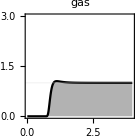
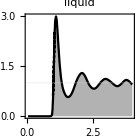
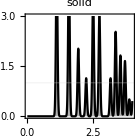

```mathematica
Row[{Plot[Exp[-(1/r^12-1/r^6)/5],{r,0,4},Filling->Axis,PlotStyle->Black,FrameLabel->{"\!\(r/a\)","\!\(ρ(r)/ρ\_∞\)"},GridLines->{None,{1}},PlotRange->{0,3},PlotRangePadding->Scaled[.02],PlotLabel->"gas",AspectRatio->1,ImageSize->140],ListLinePlot[{{0.025815813728932546,0.00008577913851359753},{0.07475915115870785,0.00008577913851359753},{0.12370248858848315,0.00008577913851359753},{0.17264582601825834,0.00008577913851359753},{0.22158916344803364,0.00008577913851359753},{0.27053250087780895,0.00008577913851359753},{0.31947583830758425,0.00008577913851359753},{0.36841917573735944,0.00008577913851359753},{0.41736251316713474,0.00008577913851359753},{0.46630585059691004,0.00008577913851359753},{0.5152491880266854,0.00008577913851359753},{0.5641925254564606,0.00008577913851359753},{0.6131358628862358,0.00008577913851359753},{0.662079200316011,0.00008577913851359753},{0.7110225377457864,0.00008577913851359753},{0.7599658751755616,0.00008577913851359753},{0.808909212605337,0.00008577913851359753},{0.8578525500351122,0.00008577913851359753},{0.9067958874648874,0.006653281921836562},{0.9407225190923454,0.05460213326119101},{0.9506542028240366,0.14342413353643835},{0.9601886192064606,0.23186389819995767},{0.9646380135182582,0.3256231084600225},{0.969087407830056,0.399292652027027},{0.9745255564333644,0.48794583157376126},{0.9779861964536516,0.5817719330658782},{0.9824355907654492,0.6823763460726351},{0.9735368021418538,0.6288633604307434},{0.986884985077247,0.8164932663376265},{0.9846602879213482,0.749267578125},{0.9923231336805554,0.9439953869885511},{0.9824355907654492,0.8803743929476351},{0.9957837737008426,1.0833892822265625},{0.9913343793890448,1.0168325063344597},{1.0002331680126402,1.2165028340107686},{0.9980084708567414,1.1479393211570947},{1.004682562324438,1.3663391938080658},{1.001716299449906,1.2924243823902026},{1.0091319566362358,1.5158410974451013},{1.0061656937617038,1.4422607421875},{1.0145701052395442,1.6699882255302176},{1.0106150880735016,1.5903133357967343},{1.0191430938377808,1.8205306594436232},{1.0135813509480336,1.7490685265343466},{1.022480139571629,1.9666880014780406},{1.0180307452598312,1.893553587767455},{1.0269295338834268,2.1158554489548145},{1.025446402446161,2.038038649000563},{1.0313789281952246,2.2526480185019},{1.0291542310393256,2.188766891891892},{1.0364639502658506,2.383324818261342},{1.0291542310393256,2.3252250052787162},{1.04027771681882,2.4994766647751265},{1.0313789281952246,2.4429535736908785},{1.0457158654221284,2.6106275953688063},{1.0506596368796814,2.7047212617891327},{1.0536258997542134,2.7725935652449323},{1.057333728347378,2.843409082911036},{1.0749829924508425,2.9304568728885134},{1.0907041856858615,2.986110377956081},{1.1159174201193818,2.883097880595439},{1.1255577744616103,2.799706811303491},{1.1301554819171347,2.7265723975929053},{1.1381643916783706,2.651654217694257},{1.1470631803019662,2.5516518257759713},{1.1559619689255616,2.4449603106524496},{1.1648607575491572,2.3345897777660474},{1.1693101518609548,2.2545878642314188},{1.1776527661955756,2.169368434596706},{1.1826583347963482,2.092978647592905},{1.1915571234199436,2.000133617504223},{1.2004559120435392,1.8978855913670367},{1.2057951852176965,1.8238083298141892},{1.2138040949789324,1.7438446398407335},{1.2191433681530897,1.673436840160473},{1.2271522779143256,1.59443829510663},{1.2360510665379212,1.503131763355152},{1.2456914208801497,1.4284365542300113},{1.2538486437851122,1.3603858741554054},{1.2620058666900746,1.2910865577491555},{1.27090465531367,1.2206277933206644},{1.2798034439372656,1.1559662690033785},{1.2919863093148072,1.08792833011583},{1.3072413755266852,1.0128190324113175},{1.3205895584620784,0.9490493911880629},{1.3361624385533706,0.8867290599926099},{1.3556903358107053,0.8212128143768771},{1.3791732502340823,0.7626458245354728},{1.4095774446980334,0.6984302417652026},{1.4451725991924156,0.6395659575591215},{1.489666542310393,0.5935934380758598},{1.5386098797401684,0.5736476888820641},{1.5875532171699436,0.583620563478962},{1.6364965545997188,0.617917522458538},{1.6809904977176964,0.6737548094969972},{1.7165856522120784,0.7320669755972489},{1.7455067152387636,0.7885104342623874},{1.7722030811095504,0.8469287769214526},{1.7988994469803368,0.9062390026745493},{1.8255958128511232,0.9673329946157097},{1.8545168758778088,1.03059298835666},{1.8856626360603927,1.0902217437861967},{1.919033093398876,1.1482737773173564},{1.959077642205056,1.205733345650338},{2.0057962824789324,1.2603165910050675},{2.0547396199087076,1.2938838274531632},{2.1036829573384828,1.2919379007025493},{2.152626294768258,1.253019365690264},{2.1971202378862356,1.19580371387012},{2.2349400895365163,1.1345610747466215},{2.2683105468749996,1.0772257329874515},{2.3016810042134828,1.0171669624947213},{2.3395008558637636,0.9573736333990239},{2.383994798981741,0.9039687547988331},{2.4329381364115163,0.8609151254414926},{2.481881473841292,0.8331856692452395},{2.530824811271067,0.8241857580236487},{2.5797681487008424,0.8339153917767197},{2.6287114861306176,0.8628610521921072},{2.6776548235603927,0.9068876449247543},{2.726598160990168,0.9567520179092441},{2.7755414984199436,1.0058866683622543},{2.8244848358497188,1.0486970568757679},{2.873428173279494,1.0849399426059585},{2.922371510709269,1.111696435426904},{2.9713148481390443,1.118507179054054},{3.02025818556882,1.1102369903639433},{3.069201522998595,1.0912642045454546},{3.1181448604283704,1.063777989193028},{3.1670881978581455,1.0321566794955466},{3.2160315352879207,1.0000488881104115},{3.2649748727176964,0.9676978558814495},{3.3139182101474716,0.9353468236524876},{3.3628615475772468,0.9112659801136362},{3.411804885007022,0.9000769012976044},{3.460748222436797,0.9076173674562344},{3.5096915598665723,0.9299955250882985},{3.558634897296348,0.9623465573172605},{3.607578234726123,1.0000488881104115},{3.6565215721558983,1.0382377005912162},{3.7054649095856735,1.0735076229460994},{3.7544082470154487,1.0881020735757065},{3.803351584445224,1.0812913299485567},{3.852294921874999,1.0557510413467441},{3.901238259304775,1.020481118991861},{3.9501815967345504,0.980589620604269},{3.988001448384831,0.9512790989231417}},Filling->Axis,PlotStyle->Black,FrameLabel->{"\!\(r/a\)","\!\(ρ(r)/ρ\_∞\)"},GridLines->{None,{1}},PlotRange->{0,3},PlotRangePadding->Scaled[.02],PlotLabel->"liquid",AspectRatio->1,ImageSize->140],
Plot[Evaluate[12Total[#2 Exp[-((r-1.122#1)/0.03)^2/2]&@@@SortBy[Tally[Cases[Norm/@Tuples[Range[-4,4],3],x_/;0<x<4]],First[N[#]]&]]/(4π r^2)],{r,0,4},Filling->Axis,PlotStyle->Black,FrameLabel->{"\!\(r/a\)","\!\(ρ(r)/ρ\_∞\)"},GridLines->{None,{1}},PlotRange->{0,3},PlotRangePadding->Scaled[.02],PlotLabel->"solid",AspectRatio->1,ImageSize->140]}]
```

Many macroscopic behaviors can be explained

| shape | volume | fluidity | compressibility
gas | × | × | high | high
liquid | × | ✓ | high | low
solid | ✓ | ✓ | low | low

#### Atomic Interaction

But why do atoms order? What is the underlying mechanism or energetic reason?

Order always arise from interaction.

Atoms (or molecules) interact in many different ways (i.e. different chemical bounds):

Ionic bound.

```mathematica
Block[{atom},
atom[col_,txt_,es_]:=Block[{r1=0.45,r2=0.7,r3=0.08},{{EdgeForm[Black],Lighter[col,0.8],Disk[{0,0},r1]},Text[Style[StringTemplate["\!\(`1`\)"][txt],SingleLetterItalics->False]],
If[Length[es]==0,{},{Circle[{0,0},r2]}],{EdgeForm[Black],Yellow,Disk[r2 ReIm@#,r3]&/@Exp[ⅈ π/4 es]}}];
Graphics[{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,-3},{0,0},{-4,3}}]]}}],Translate[{Translate[atom[Gray,"Na",{0}],{-1,0}],Text["+"],{Red,Arrow[BSplineCurve[{{-0.2,0.2},{0,0.4},{0.2,0.2}}]]},Translate[atom[Gray,"Cl",{-0.25,0.25,1.75,2.25,4,5.75,6.25}],{1,0}]},{-2,0}],Text["→"],
Translate[{Translate[atom[Red,"Na\^+",{}],{-1,0}],{AbsoluteThickness[1],Translate[Line[{0,#}&/@{-0.1,0.1}],{#,0}]&/@Range[-0.35,0.1,0.2]},Translate[atom[Blue,"Cl\^-",{-0.25,0.25,1.75,2.25,3.75,4.25,5.75,6.25}],{1,0}]},{1.8,0}]},PlotRange->{All,{-1,1}},ImageSize->{Automatic,60}]]
```

-Graphics-

Covalent bound.

```mathematica
Block[{atom},
atom[col_,txt_,es_]:=Block[{r1=0.45,r2=0.7,r3=0.08},{{EdgeForm[Black],Lighter[col,0.8],Disk[{0,0},r1]},Text[Style[StringTemplate["\!\(`1`\)"][txt],SingleLetterItalics->False]],
{Circle[{0,0},r2]},{EdgeForm[Black],Yellow,Disk[r2 ReIm@#,r3]&/@Exp[ⅈ π/4 es]}}];
Graphics[{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,-3},{0,0},{-4,3}}]]}}],Translate[{Translate[atom[Gray,"H",{0}],{-1,0}],Text["+"],{Red,Rotate[Arrow[BSplineCurve[{{-0.2,0.2},{0,0.4},{0.2,0.2}}]],#,{0,0}]&/@{0,π}},Translate[atom[Gray,"H",{4}],{1,0}]},{-2,0}],Text["→"],
Translate[{Translate[atom[Gray,"H",{}],{-0.7,0}],Translate[atom[Gray,"H",{3.75,4.25}],{0.7,0}]},{1.7,0}]},PlotRange->{All,{-1,1}},ImageSize->{Automatic,60}]]
```

-Graphics-

Metallic bound.

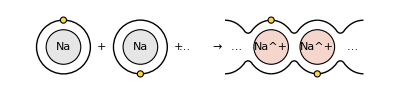

```mathematica
Block[{r1=0.45,r2=0.7,r3=0.08,atom},
atom[col_,txt_,es_]:={{EdgeForm[Black],Lighter[col,0.8],Disk[{0,0},r1]},Text[Style[StringTemplate["\!\(`1`\)"][txt],SingleLetterItalics->False]],
If[Length[es]==0,{},{Circle[{0,0},r2]}],{EdgeForm[Black],Yellow,Disk[r2 ReIm@#,r3]&/@Exp[ⅈ π/4 es]}};
Graphics[{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,-3},{0,0},{-4,3}}]]}}],Translate[{Translate[atom[Gray,"Na",{2}],{-1,0}],Text["+"],Translate[atom[Gray,"Na",{-2}],{1,0}],Text["+",{2,0}],Text["…",{2,0},{-2,0}]},{-3,0}],Text["→"],
Block[{x1,x2,softmax},
{x1,x2}={-0.6,0.6};
softmax[ys_]:=(#.ys/Total[#])&@Exp[4ys];
Translate[{Translate[atom[Red,"Na\^+",{}],{x1,0}],Translate[atom[Red,"Na\^+",{}],{x2,0}],Text["…",{-1.5,0}],Text["…",{1.5,0}],{Translate[Rotate[Line[Table[{x,softmax[Re[#]-Im[#]^2&@Sqrt[r2^2-(x-{x1,x2})^2]]},{x,x1,x2,(x2-x1)/100}]],#,{0,0}]&/@{0,π},{#,0}]&/@{-2x2,0,2x2},
{EdgeForm[Black],Yellow,Disk[#,r3]&/@{{x1,r2},{x2,-r2}}}}},{2,0}]]},PlotRange->{All,{-1,1}},ImageSize->{Automatic,60}]]
```

Hydrogen bound.

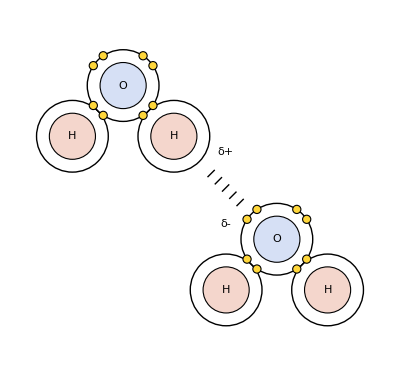

```mathematica
Block[{r1=0.45,r2=0.7,r3=0.08,atom,H2O},
atom[col_,txt_,es_]:={{EdgeForm[Black],Lighter[col,0.8],Disk[{0,0},r1]},Text[Style[StringTemplate["\!\(`1`\)"][txt],SingleLetterItalics->False]],
{Circle[{0,0},r2]},{EdgeForm[Black],Yellow,Disk[r2 ReIm@#,r3]&/@Exp[ⅈ π/4 es]}};
H2O={Translate[atom[Red,"H",{}],2r2{1,-1}/Sqrt[2]],Translate[atom[Red,"H",{}],2r2{-1,-1}/Sqrt[2]],atom[Blue,"O",{0.75,1.25,2.75,3.25,4.75,5.25,6.75,7.25}]};
Graphics[{Translate[H2O,{-1.5,1.5}],Translate[H2O,{1.5,-1.5}],{Translate[{AbsoluteThickness[1],Rotate[Translate[Line[{0,#}&/@{-0.1,0.1}],{#,0}]&/@Range[-0.4,0.4,0.2],-π/4,{0,0}],Text["δ+",{0.,0.7}],Text["δ-",{0.,-0.7}]},{1,-1}/2]}},PlotRange->{All,{-3.5,2.5}},ImageSize->{Automatic,150}]]
```

Van der Waals force (Molecular bound).

```mathematica
Block[{mol,efield},
mol={First@ContourPlot[y,{x,-1,1},{y,-1,1},ColorFunction->(Lighter[ColorData["BlueRedSplit"][#]]&),ContourStyle->None,RegionFunction->(#1^2+#2^2<=1&),BoundaryStyle->Black],{Red,Text[Style["+",Bold],#]&/@ReIm[1.25Exp[ⅈ π/2(1+0.3 Range[-1,1])]]},{Blue,Text[Style["-",Bold],#]&/@ReIm[1.25Exp[-ⅈ π/2(1+0.3 Range[-1,1])]]}};
efield={First@ContourPlot[Re[1/(x+ⅈ y)],{x,-6,6},{y,-6,6},ContourLabels->None,ContourStyle->AbsoluteThickness[1],Contours->7,ContourShading->None],{AbsoluteThickness[1],Translate[Rotate[Line[Offset/@{{-4,3},{0,0},{-4,-3}}],#1,{0,0}],#2]&@@@{{π/2,{0,2}},{π/2,{0,-2}},{-π/2,{-1.96,0}},{-π/2,{1.96,0}},{-π/2,{2.94,0}},{0,{3,2.94}},{π,{3,-2.94}}}}};
Graphics[{Translate[efield,{-3,0}],Translate[mol,{-3,0}],Translate[Rotate[mol,π,{0,0}],{3,0}]},PlotRange->{{-5.2,5.2},{-3.2,3.2}},ImageSize->180]]
```

-Graphics-

All types of atomic forces are the residual of the electrostatic force of electrons and nuclei.

They are generally repulsive at short range, and attractive at longer range. The pair-wise interaction can be described by the inter-atomic potential energy V(r) (where r is the inter-atom distance). One famous phenomenological model (the 6-12 potential) is

V(r)=V_0(1/(r/a)^12-2/(r/a)^6).

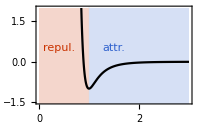

```mathematica
Plot[1/r^12-2/r^6,{r,0,3},PlotStyle->Black,PlotRange->{-1.5,2},FrameLabel->{"\!\(r/a\)","\!\(V(r)/V\_0\)"},GridLines->{{1},None},Prolog->{{{Lighter[Red,0.8],Rectangle[{0,-2},{1,2}]},{Red,Text["repul.",{0.4,0.5}]}},{{Lighter[Blue,0.8],Rectangle[{1,-2},{3,2}]},{Blue,Text["attr.",{1.5,0.5}]}}},ImageSize->200]
```

They can be isotropic (ionic bounds, metallic bounds, Van der Waals) or directional (most covalent bounds, hydrogen bounds).

#### Statistical Mechanics of Atoms

Consider a collection of atoms interacting with each other.

Let r_i be the position of the ith atom.

The total potential energy of all atoms is

V(r_1,r_2,…)=∑_(i≠j) V(r_i-r_j),

(summing the potential energy over all pairs of atoms).

For isotropic interaction, V(r) only depends on r=|r|, and is often denoted as V(r).

For directional interaction, V(r) also depends on the direction of r. [But we generally assume the inversion symmetry V(r)=V(-r), i.e. the action and reaction are always equal in magnitude and opposite in direction (Newton’s third law).]

By Boltzmann distribution, the probability (density) to observe the atoms at positions {r_i} is given by

p(r_1,r_2,…)=1/Z exp(-(V(r_1,r_2,…))/(k_B T)),
Z=∫ⅆ r_1ⅆ r_2… exp(-(V(r_1,r_2,…))/(k_B T)).

k_B - Boltzmann constant, T - temperature.

High-temperature limit (T→∞): p(r_1,r_2,…)=1/Z. The atoms can appear anywhere with equal probability independently. ⇒ Gas phase.

Low-temperature limit (T->0): the probability is dominated by the configuration of the lowest energy. The atoms will arrange themselves to minimize the total potential energy

min_{r_i} V(r_1,r_2,…).

This leads to crystal formation. ⇒ Solid phase.

#### Minimal Energy Configurations

##### Isotropic Repulsive Interaction

Inter-atomic potential:

V(r)=V_0/(r/a)^12.

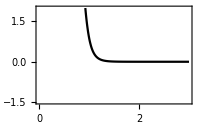

```mathematica
Plot[1/(0.1+r^12),{r,0,3},PlotStyle->Black,PlotRange->{-1.5,2},FrameLabel->{"\!\(r/a\)","\!\(V(r)/V\_0\)"},ImageSize->200]
```

Searching for minimal energy configurations ...

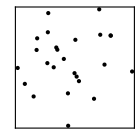

```mathematica
Block[{L=20,V,U,rs0,plt,U0,sol},
V=Function[{Typed[r,"Real64"]},(1)/(0.1+r^12)];
U[rs_List]:=Total[V[Norm[#1-#2]]&@@@Subsets[rs,{2}]];
rs0=Flatten[Table[{x,y}+RandomReal[{-0.2,0.2},2],{x,-2,2},{y,-2,2}],1];
plt[rs_List]:=Graphics[Point[rs],PlotRange->L/2,Frame->True,FrameTicks->None,ImageSize->140];
{U0,sol}=Monitor[FindMinimum[U[rs],{{rs,rs0}},Method->"QuasiNewton",AccuracyGoal->3,MaxIterations->1000],plt[rs]];plt[rs/.sol]]
```

Observation: under purely repulsive interaction, all atoms fly apart (if not restricted by a container). → Doesn’t look physical.

##### Isotropic Attractive Interaction

Inter-atomic potential:

V(r)=-(2 V_0)/(r/a)^6.

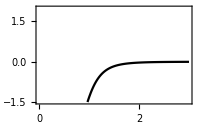

```mathematica
Plot[-2/(0.5+r^6),{r,0,3},PlotStyle->Black,PlotRange->{-1.5,2},FrameLabel->{"\!\(r/a\)","\!\(V(r)/V\_0\)"},ImageSize->200]
```

Searching for minimal energy configurations ...

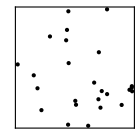

```mathematica
Block[{L=20,V,U,rs0,plt,U0,sol},
V=Function[{Typed[r,"Real64"]},-2/(0.5+r^6)];
U[rs_List]:=Total[V[Norm[#1-#2]]&@@@Subsets[rs,{2}]];
rs0=Flatten[Table[{x,y}+RandomReal[{-0.2,0.2},2],{x,-2,2},{y,-2,2}],1];
plt[rs_List]:=Graphics[Point[rs],PlotRange->L/2,Frame->True,FrameTicks->None,ImageSize->140];
{U0,sol}=Monitor[FindMinimum[U[rs],{{rs,rs0}},Method->"QuasiNewton",AccuracyGoal->3,MaxIterations->1000],plt[rs]];plt[rs/.sol]]
```

Observation: under purely attractive interaction, all atoms will collapse to a single point and takes up no volume (this could happen for a black-hole). → Doesn’t look physical either.

##### Isotropic Interaction with Both Attraction and Repulsion

Inter-atomic potential:

V(r)=V_0(1/(r/a)^12-2/(r/a)^6).

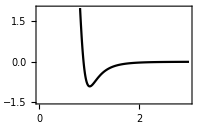

```mathematica
Plot[(1-2r^6)/(0.1+r^12),{r,0,3},PlotStyle->Black,PlotRange->{-1.5,2},FrameLabel->{"\!\(r/a\)","\!\(V(r)/V\_0\)"},ImageSize->200]
```

Searching for minimal energy configurations ...

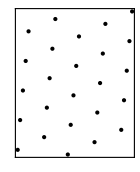

```mathematica
Block[{L=20,V,U,rs0,plt,U0,sol},
V=Function[{Typed[r,"Real64"]},(1-2r^6)/(0.1+r^12)];
U[rs_List]:=Total[V[Norm[#1-#2]]&@@@Subsets[rs,{2}]];
rs0=Flatten[Table[{x,y}+RandomReal[{-0.2,0.2},2],{x,-2,2},{y,-2,2}],1];
plt[rs_List]:=Graphics[Point[rs],PlotRange->L/2,Frame->True,FrameTicks->None,ImageSize->140];
{U0,sol}=Monitor[FindMinimum[U[rs],{{rs,rs0}},Method->"QuasiNewton",AccuracyGoal->3,MaxIterations->1000],plt[rs]];plt[rs/.sol]]
```

A crystal is formed at low-temperature!

Observation:

Need short-range repulsion + long-range attraction to crystalize.
⇒ The existence of crystals implies that the inter-atomic interaction is neither purely repulsive (unlike electric force) nor purely attractive (unlike gravity).

We can infer microscopic laws of physics by observing their macroscopic consequences.

The crystal aways have roughly the same volume.

Because the atomic spacing is determined by the equilibrium position r=a of the inter-atomic potential (the distance where interaction switch from repulsive to attractive). ⇒ Explains why a solid is hard to compress.

The crystal aways assume the same triangular lattice structure.

Because triangular lattice is the closest packed structure in 2D.

Spontaneous symmetry breaking: although the microscopic interaction is isotropic (continuous rotation symmetry, no special bound angle), the resulting low-energy configuration (the crystal lattice) spontaneously breaks the continuous rotation symmetry to a discrete (6-fold) rotation symmetry with an emergent  30° bound angle. ⇒ Explains why a solid is rigid (has a fixed shape).

This is an emergent phenomenon. No where in the microscopic theory can we see why 30° bound angle should be special. ⇒ Demonstrates that reductionism doesn’t always work.

##### Directional Interaction

How can we realize other lattice structures? - Need directional inter-atomic interactions. Consider

V(r)=V_0(1/(r/a)^12-(1+cos 4θ)/(r/a)^6),

where r,θ is the polar representation of r=r(cos θ, sin θ).

```mathematica
Row@{Plot3D[Block[{r=Norm[{x,y}],θ=ArcTan[x,y]},(1-(1+Cos[4θ])r^6)/(0.1+r^12)],{x,-2,2},{y,-2,2},PlotRange->{-1,1},PlotPoints->32,ClippingStyle->None,ColorFunction->"BlueRedSplit",MeshFunctions->{#3&},AxesLabel->(Style[#,FontFamily->"LaTeX"]&/@{"\!\(,x\)","\!\(,y\)","\!\(V\)"}),TicksStyle->Directive[FontFamily->"LaTeX"],BoxRatios->{1, 1, 1},ViewPoint->{0.8,-2,0.4},ImageSize->180],
ContourPlot[Block[{r=Norm[{x,y}],θ=ArcTan[x,y]},(1-(1+Cos[4θ])r^6)/(0.1+r^12)],{x,-2,2},{y,-2,2},Contours->64,ContourStyle->None,PlotLabel->"top view",PlotRange->{-1,1},ClippingStyle->None,FrameLabel->{"\!\(,x\)","\!\(,y\)"},ImageSize->140]}
```

-Graphics3D--Graphics-

Searching for minimal energy configurations ...

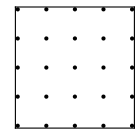

```mathematica
Block[{L=20,V,U,rs0,plt,U0,sol},
V[{x_,y_}]:=Block[{r=Norm[{x,y}],θ=ArcTan[x,y]},(1-(1+Cos[4θ])r^6)/(0.1+r^12)];
U[rs_List]:=Total[V[#1-#2]&@@@Subsets[rs,{2}]];
rs0=Flatten[Table[{x,y}+RandomReal[{-0.3,0.3},2],{x,-2,2},{y,-2,2}],1];
plt[rs_List]:=Graphics[Point[rs],PlotRange->L/2,Frame->True,FrameTicks->None,ImageSize->140];
{U0,sol}=Monitor[FindMinimum[U[rs],{{rs,rs0}},Method->"QuasiNewton",AccuracyGoal->3,MaxIterations->1000],plt[rs]];plt[rs/.sol]]
```

A square lattice crystal is formed at low-temperature!

Observations:

The explicit symmetry breaking in the microscopic inter-atomic potential already breaks the continuous rotation symmetry to 4-fold discrete rotation symmetry.

The square lattice is compatible with the 4-fold rotation symmetry and gains energy from bounds in all four directions.

The triangular lattice is incompatible with the 4-fold rotation symmetry, and can not gain as much energy, thus it ceases to be the minimal energy configuration.

Given the atomic spacing a=1 as unit length, show that the volume V of the triangular lattice scales as the number N of sites as V=(√3/2)N≈0.866N, whereas for square lattice, the scaling is V=N. This verifies that the triangular lattice is at least closer packed compared to square lattice.

#### Gas-Solid Transition

How does temperature drives the gas-solid transition?

Consider a canonical ensemble of atoms specified by (N,V,T)

N: number of atoms in the system,

V: volume of the system,

T: temperature of the system (in equilibrium with a thermal bath).

The equilibrium state is determined by minimizing the free energy F

F=E-T S,

E: total energy of the system,

S: entropy of the system,

S=k_B ln Ω,

Ω: number of microscopic configurations

Gas phase: every atom can reach every point in the space, number of configurations for a single atom ∝V, number of configurations for N atoms ∝V^N; however, permutations of atoms does not leads to new configurations, thus a factor N!  must be divided,

Ω_gas=V^N/(N!)
⇒S_gas=k_B(N ln V-ln N!)
≃k_B(N ln V-N ln N+N)

Solid phase: every atom typically travels within the V/N volume surrounding its equilibrium position on the lattice, total number of configurations ∝(V/N)^N. Moreover, atoms are distinguishable by their lattice coordinates, hence there is no permutation redundance.

Ω_solid=(V/N)^N
⇒S_solid=k_B(N ln V-N ln N)

Free energy difference

F_gas-F_solid
=(E_gas-E_solid)-T(S_gas-S_solid)
=E_bind-N k_B T

E_bind is the binding energy, i.e. the energy released when atoms binds to solid. It defines a temperature scale

T_*=E_bind/(N k_B).

When T<T_*, F_gas>F_solid, the system is in the solid phase,

When T>T_*, F_gas<F_solid, the system is in the gas phase,

Therefore T_* is the gas-solid transition temperature.

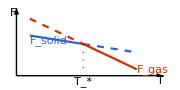

```mathematica
Block[{Fgas,Fsolid},
Fgas[T_]:=3-1.5T;
Fsolid[T_]:=2-0.5T;
Graphics[{AbsoluteThickness[1],{Arrowheads[0.05],{Arrow[{{0,0},#1}],Text["\!\("<>#2<>"\)",#1,#3]}&@@@{{{2.2,0},"T",{1,1.2}},{{0,3.2},"F",{2,1}}}},
First@Plot[{Fsolid[T],Fgas[T]},{T,0.2,1},PlotStyle->{Blue,Directive[Red,Dashed]}],
First@Plot[{Fsolid[T],Fgas[T]},{T,1,1.8},PlotStyle->{Directive[Blue,Dashed],Red}],
{Blue,Text["\!\(F\_solid\)",{0.2,Fsolid[0.2]},{-0.5,1.2}]},{Red,Text["\!\(F\_gas\)",{1.8,Fgas[1.8]},{-1.2,-0.2}]},
{Dotted,Line[{1,#}&/@{0,1.5}],Text["\!\(T\_*\)",{1,0},{0,1.2}]}},AspectRatio->0.5,ImageSize->180]]
```

The transition is generally a first order transition, because the first order derivative of the free energy ∂F/∂T is discontinuous at the transition.

Note: this simple argument assumes that each atom fluctuates in a mean-field potential, which is not valid in 1D and 2D. In low dimensions, collective fluctuations of atoms will destroy the crystal order (to be discussed later).

### Lattice Structure

#### Lattice

Lattice: a collection of repeating sets of points in the space. Each lattice point is called a site.

A simple math model of lattice is a set of points as integer combinations of linearly independent primitive lattice vectors a_i.

1D (n∈ℤ)

R_n=n a.

2D (n_1,n_2∈ℤ)

R_n=n_1 a_1+n_2 a_2.

3D (n_1,n_2,n_3∈ℤ)

R_n=n_1 a_1+n_2 a_2+n_3 a_3.

Bravais lattice in dimension D is described by

R_n=∑_(i=1)^D n_i a_i.

Closure: if R_n and R_m are two sites on the Bravais lattice, R_n+R_m=R_(n+m) is also a site.

Homogeneity: every site on the Bravais lattice is equivalent. We can start with a representative site (say R_0=0) and reach all the other sites by translation.

General lattice (inhomogeneous): if the repeating structure contains more than one site, different types of sites (labeled by s) are further translated by different sub-lattice vectors r_s.

R_(n,s)=R_n+r_s.

Examples:

Chain lattice (1D) (n∈ℤ)

a=1.

R_n=n a=n.

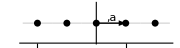

```mathematica
Graphics[{Table[Translate[{{LightGray,AbsoluteThickness[1],Line[{{-0.5,0},{0.5,0}}]},{Black,AbsolutePointSize[5],Point[{0,0}]}},{n,0}],{n,-2,2}],
{Arrowheads[0.06],Arrow[{{0,0},{1,0}}]},Text["\!\(,a\)",{0.5,0},{0,-1}]},Axes->{True,False},AxesOrigin->{0,-1},Ticks->{Range[-2,2],None},
AspectRatio->0.2,ImageSize->180]
```

Square lattice (2D) (n_1,n_2∈ℤ)

{ | a_1=(1,0)
a_2=(0,1).

R_n=n_1 a_1+n_2 a_2=(n_1,n_2).

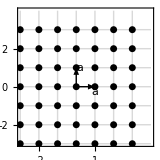

```mathematica
Block[{L=2,a1,a2,Rs},
a1={1,0};
a2={0,1};
Rs=Tuples[Range[-L-1,L+1],2].{a1,a2};
Graphics[{{LightGray,AbsoluteThickness[1],Translate[Line[{{0,0},#}]&/@{a1,a2},#]&/@Rs},{Black,AbsolutePointSize[5],Point[Rs]},{Arrowheads[0.06],{Arrow[{{0,0},#1}],Text[StringTemplate["\!\(\*StyleBox[\"a\",Bold]\_`1`\)"][#2],#1,#3]}&@@@{{a1,"1",{0,0.8}},{a2,"2",{-1.4,0.2}}}}},PlotRange->L,PlotRangeClipping->True,PlotRangePadding->0.5,Frame->True,FrameTicks->{{Range[-L,L],{#,""}&/@Range[-L,L]},{Range[-L,L],{#,""}&/@Range[-L,L]}},ImagePadding->{{Automatic, 5}, {Automatic, 5}},ImageSize->160]]
```

Triangular lattice (2D) (n_1,n_2∈ℤ)

{ | a_1=(1,0)
a_2=(1/2,(√3)/2).

R_n=n_1 a_1+n_2 a_2=(n_1+n_2/2,(n_2 √3)/2).

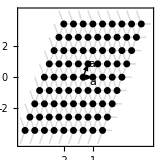

```mathematica
Block[{L=2,a1,a2,Rs},
a1={1,0};
a2={1,Sqrt[3]}/2;
Rs=Tuples[Range[-2L,2L],2].{a1,a2};
Graphics[{{LightGray,AbsoluteThickness[1],Translate[Line[{{0,0},#}]&/@CirclePoints[{1,0},3],#]&/@Rs},{Black,AbsolutePointSize[5],Point[Rs]},{Arrowheads[0.06],{Arrow[{{0,0},#1}],Text[StringTemplate["\!\(\*StyleBox[\"a\",Bold]\_`1`\)"][#2],#1,#3]}&@@@{{a1,"1",{0,0.8}},{a2,"2",{-1.4,0.2}}}}},PlotRange->L,PlotRangeClipping->True,PlotRangePadding->0.5,Frame->True,FrameTicks->{{Range[-L,L],{#,""}&/@Range[-L,L]},{Range[-L,L],{#,""}&/@Range[-L,L]}},ImagePadding->{{Automatic, 5}, {Automatic, 5}},ImageSize->160]]
```

Honeycomb lattice (2D) (n_1,n_2∈ℤ)

{ | a_1=(√3,0)
a_2=((√3)/2,3/2),{ | r_A=(√3,1)
r_B=((√3)/2,1/2).

R_(n,A)=n_1 a_1+n_2 a_2+r_A
=(√3 n_1+(√3 n_2)/2+√3,(3 n_2)/2+1),
R_(n,B)=n_1 a_1+n_2 a_2+r_B
=(√3 n_1+(√3 n_2)/2+(√3)/2,(3 n_2)/2+1/2).

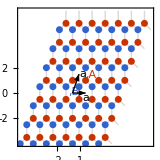

```mathematica
Block[{L=1,a1,a2,Rs},
a1={Sqrt[3],0};
a2={Sqrt[3],3}/2;
Rs=Tuples[Range[-L-2,L+2],2].{a1,a2};
Graphics[{{LightGray,AbsoluteThickness[1],Translate[Line[{{0,0},#}]&/@CirclePoints[{1,π/2},3],#+{Sqrt[3],1}]&/@Rs},{AbsolutePointSize[5],Blue,Point[#+{Sqrt[3]/2,1/2}&/@Rs],Red,Point[#+{Sqrt[3],1}&/@Rs]},{Arrowheads[0.06],{Arrow[{{0,0},#1}],Text[StringTemplate["\!\(\*StyleBox[\"a\",Bold]\_`1`\)"][#2],#1,#3]}&@@@{{a1,"1",{0,0.8}},{a2,"2",{-1.,-0.2}}}},
{Blue,Text["\!\(,B\)",{Sqrt[3]/2,1/2},{1.5,0.5}],Red,Text["\!\(,A\)",{Sqrt[3],1},{-1.5,-0.5}]}},PlotRange->2L,PlotRangeClipping->True,PlotRangePadding->0.8,Frame->True,FrameTicks->{{Range[-2L,2L],{#,""}&/@Range[-2L,2L]},{Range[-2L,2L],{#,""}&/@Range[-2L,2L]}},ImagePadding->{{Automatic, 5}, {Automatic, 5}},ImageSize->160]]
```

Cubic lattice (3D) (n_1,n_2,n_3∈ℤ)

{ | a_1=(1,0,0)
a_2=(0,1,0)
a_3=(0,0,1).

R_n=n_1 a_1+n_2 a_2+n_3 a_3=(n_1,n_2,n_3).

```mathematica
Block[{L=1,a1,a2,a3,Rs},
a1={1,0,0};
a2={0,1,0};
a3={0,0,1};
Rs=Tuples[Range[-2L,2L],3].{a1,a2,a3};
Graphics3D[{Translate[{{Black,Sphere[{0,0,0},0.08]},{Black,Opacity[0.2],Tube[{{0,0,0},#},0.01]&/@{a1,a2,a3}}},#]&/@Rs,
{Black,Arrowheads[0.05],Arrow[Tube[{{0,0,0},#},0.02]]&/@{a1,a2,a3}},{Text[StringTemplate["\!\(\*StyleBox[\"a\",Bold]\_`1`\)"][#2],#1,#3]&@@@{{a1,1,{-1,1}},{a2,2,{1,-1}},{a3,3,{-1.2,1}}}}},PlotRange->L,PlotRangePadding->0.5,Axes->True,Ticks->{Range[-L,L],Range[-L,L],Range[-L,L]},Lighting->"Neutral",ViewPoint->{4,1,1},ImageSize->180]]
```

-Graphics3D-

Diamond lattice (3D) (n_1,n_2,n_3∈ℤ)

{ | a_1=(1,1,0)
a_2=(0,1,1)
a_3=(1,0,1),{ | r_A=(0,0,0)
r_B=(1/2,1/2,1/2).

R_(n,A)=n_1 a_1+n_2 a_2+n_3 a_3+r_A
=(n_1+n_3,n_1+n_2,n_2+n_3),
R_(n,B)=n_1 a_1+n_2 a_2+n_3 a_3+r_B
=(n_1+n_3+1/2,n_1+n_2+1/2,n_2+n_3+1/2).

```mathematica
Block[{L=1,a1,a2,a3,RAs,RBs},
a1={1,1,0};
a2={0,1,1};
a3={1,0,1};
RAs=Tuples[Range[-2L,2L],3].{a1,a2,a3};
RBs=#+{1,1,1}/2&/@RAs;
Graphics3D[{{Red,Sphere[#,0.1]&/@RAs,Blue,Sphere[#,0.1]&/@RBs},{Gray,Translate[Tube[{{0,0,0},#}&/@{{1,-1,1},{-1,1,1},{1,1,-1},{-1,-1,-1}}/2,0.015],#]&/@RBs},
{Black,Arrowheads[0.06],Arrow[Tube[{{0,0,0},#},0.02]]&/@{a1,a2,a3}},
{Text[StringTemplate["\!\(\*StyleBox[\"a\",Bold]\_`1`\)"][#2],#1,#3]&@@@{{a1,1,{0,1}},{a2,2,{1.5,-0.2}},{a3,3,{-1,1}}}},{Translate[GraphicsComplex[{{0,0,0},a1,a2,a3},{Opacity[0.2],EdgeForm[None],Polygon[{{1,2,3},{1,3,4},{1,2,4},{2,3,4}}]}],#]&/@{{0,0,0},-a1,-a2,-a3}},
{Red,Text["\!\(,A\)",{0,0,0},{0.2,-1}],Blue,Text["\!\(,B\)",{1,1,1}/2,{0,1.2}]}},PlotRange->L,PlotRangePadding->0.2,Axes->True,Ticks->{Range[-L,L],Range[-L,L],Range[-L,L]},Lighting->"Neutral",ViewPoint->{2 ,-5,1},ImageSize->180]]
```

-Graphics3D-

#### Unit Cell

Unit cell: the repeated building block of the lattice, which can tile the full space under lattice translation.

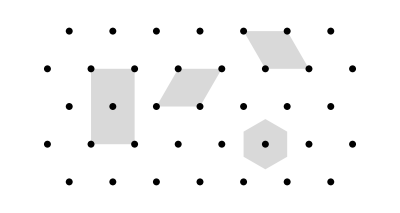

```mathematica
Block[{Rs},
Rs=Tuples[{Range[-5,5],Range[-3,3]}].{{1,0},{1,Sqrt[3]}/2};
Graphics[{{LightGray,Parallelogram[{-5/2,-Sqrt[3]/2},{{1,0},{0,Sqrt[3]}}],Parallelogram[{-1,0},{{1,0},{1/2,Sqrt[3]/2}}],Parallelogram[{3/2,Sqrt[3]/2},{{1,0},{-1/2,Sqrt[3]/2}}],Translate[Polygon[CirclePoints[{1/Sqrt[3],π/6},6]],{3/2,-Sqrt[3]/2}]},{Black,AbsolutePointSize[5],Point[Rs]}},PlotRange->{{-3.75,3.75},{-2,2}}]]
```

Primitive unit cell: a unit cell of minimal volume, e.g. parallelogram (parallelepiped) spanned by primitive lattice vectors a_i.

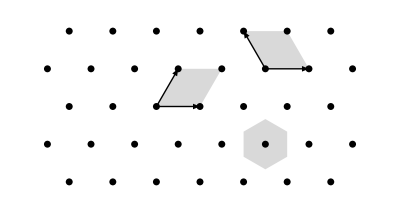

```mathematica
Block[{Rs,puc},
Rs=Tuples[{Range[-5,5],Range[-3,3]}].{{1,0},{1,Sqrt[3]}/2};
puc[p_,vs_]:={Parallelogram[p,vs],{Black,Translate[Arrow[{{0,0},#}&/@vs],p]}};
Graphics[{{LightGray,puc[{-1,0},{{1,0},{1/2,Sqrt[3]/2}}],puc[{3/2,Sqrt[3]/2},{{1,0},{-1/2,Sqrt[3]/2}}],Translate[Polygon[CirclePoints[{1/Sqrt[3],π/6},6]],{3/2,-Sqrt[3]/2}]},{Black,AbsolutePointSize[5],Point[Rs]}},PlotRange->{{-3.75,3.75},{-2,2}}]]
```

The choice of primitive lattice vectors for a lattice is not unique, hence the primitive unit cell is also not unique.

However, the volume of the primitive unit cell is unique, which is given by the absolute value of the determinant of the matrix A formed by all primitive lattice vectors (see Wikipedia Parallelepiped:Volume)

Ω=|det A|,
A=(a_1
a_2
…).

In 2D, Ω=|a_1×a_2|.

In 3D, Ω=|a_1·(a_2×a_3)|.

Calculate the volume of primitive unit cell for the triangular lattice defined in Eq. (DisplayFormulaNumbered).

Arrange the primitive lattice vectors to a matrix

{ | a_1=(1,0)
a_2=(1/2,(√3)/2)⇒(a_1
a_2)=(1 | 0
1/2 | (√3)/2),

then the primitive unit cell volume is given by the determinant

Ω=det(1 | 0
1/2 | (√3)/2)=(√3)/2.

Wigner-Seitz cell (Voronoi cell): a primitive unit cell enclosed by perpendicular bisectors between a Bravais lattice point and all its neighbors.

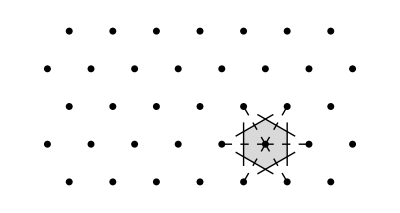

```mathematica
Block[{Rs,puc},
Rs=Tuples[{Range[-5,5],Range[-3,3]}].{{1,0},{1,Sqrt[3]}/2};
Graphics[{{Translate[{LightGray,Polygon[CirclePoints[{1/Sqrt[3],π/6},6]],{Black,Dashing[{0.015,0.015},0.002],Line[{{0,0},#}&/@CirclePoints[6]]},{Black,AbsoluteThickness[1],Rotate[Line[{{1/2,-1/2},{1/2,1/2}}],# π/3,{0,0}]&/@Range[6]}},{3/2,-Sqrt[3]/2}]},,{Black,AbsolutePointSize[5],Point[Rs]}},PlotRange->{{-3.75,3.75},{-2,2}}]]
```

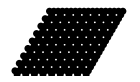
Calculate the volume of primitive unit cell for the Kagome lattice (figure below), assuming that the nearest neighbor links are all of unit length. [Hint: first find the primitive lattice vectors and then use Eq. (DisplayFormulaNumbered)]
-Graphics-

#### Lattice Symmetry

Lattice symmetry: coordinate transformations which leave the lattice  invariant.

General form of coordinate transformation (affine transformation)

R→R'=R A+b,

where

A - matrix (to implement rotations, reflections, inversions),

b - vector (to implement translation).

##### Translation Symmetry

Every lattice (by definition) is invariant under the translation by any Bravais lattice vector (i.e. b=R_m).

R_(n,s)→R'_(n,s)=R_(n,s)+R_m=R_(n+m,s)

##### Point Group Symmetry

Lattice symmetry that preserves a fixed point.

Rotation by angle θ along an axis. The rotation is said to be k-fold if the angle is θ=2π/k. In 2D, rotation axis reduces to a point, and the rotation about the origin is implemented by

R→R(cos θ | sin θ
-sin θ | cos θ).

In 3D, a rotation about axis N (specified by a unit vector) by θ angle is implemented by

R→R cos θ+(R·N)N(1-cos θ)+N×R sin θ.

Reflection about a mirror plane (in 3D; reduces to a line in 2D). The mirror plane can be specified by the normal vector N (the unit vector perpendicular to the mirror plane).

R→R-2(R·N)N.

Show the composition of two reflections induced by normal vectors N_1 and N_2 is a rotation along the axis (N_1×N_2)/sin θ by the angle 2θ, where θ is the angle between N_1 and N_2 (i.e. N_1·N_2=cos θ).

According to Eq. (DisplayFormulaNumbered), any point transforms under two reflections as

R→R-2(R·N_1)N_1
→(R-2(R·N_1)N_1)-2((R-2(R·N_1)N_1)·N_2)N_2
=R-2(R·N_1)N_1-2(R·N_2)N_2+4(R·N_1)(N_1·N_2)N_2.

On the other hand, according to Eq. (DisplayFormulaNumbered), a rotation about N_1×N_2 by an angle θ is given by

R→R cos 2θ+R·(N_1×N_2)(N_1×N_2)(1-cos 2θ)/(sin^2 θ)+(N_1×N_2)×R (sin 2θ)/(sin θ)
=R (2 cos^2 θ-1)+2R·(N_1×N_2)(N_1×N_2)+2R×(N_1×N_2) cos θ
=R (2 (N_1·N_2)^2-1)+2R·(N_1×N_2)(N_1×N_2)+2 (N_1·N_2)(N_1×N_2)×R

To simplify, consider decomposing R to component R_(||) that lies in the plane spanned by N_1 and N_2, and R_⊥ that is perpendicular to the plane.

R=R_(||)+R_⊥.

The perpendicular component is simply given by

R_⊥=1/(sin^2 θ)R·(N_1×N_2)(N_1×N_2)
=(R·(N_1×N_2)(N_1×N_2))/(1-(N_1·N_2)^2).

The parallel component must be a linear combination of N_1 and N_2

R_(||)=x_1 N_1+x_2 N_2,

such that

R·N_1=R_(||)·N_1=x_1+x_2(N_1·N_2),
R·N_2=R_(||)·N_2=x_2+x_1(N_1·N_2),

from which the solution of x_1 and x_2 is

x_1=(R·N_1-(N_1·N_2)(R·N_2))/(1-(N_1·N_2)^2),
x_2=(R·N_2-(N_1·N_2)(R·N_1))/(1-(N_1·N_2)^2),

thus

R_(||)=1/(1-(N_1·N_2)^2)((R·N_1-(N_1·N_2)(R·N_2))N_1+(R·N_2-(N_1·N_2)(R·N_1))N_2).

Substitute Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) into Eq. (DisplayFormulaNumbered), we obtain

R(1-(N_1·N_2)^2)=(R·N_1-(N_1·N_2)(R·N_2))N_1+(R·N_2-(N_1·N_2)(R·N_1))N_2+R·(N_1×N_2)(N_1×N_2).

We also have the identity

(N_1×N_2)×R=(R·N_1)N_2-(R·N_2)N_1.

Substitute Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) into Eq. (DisplayFormulaNumbered), we have

R→R (2 (N_1·N_2)^2-1)+2(R(1-(N_1·N_2)^2)-(R·N_1-(N_1·N_2)(R·N_2))N_1-(R·N_2-(N_1·N_2)(R·N_1))N_2)+2 (N_1·N_2)((R·N_1)N_2-(R·N_2)N_1)
= R-2(R·N_1)N_1-2(R·N_2)N_2+4 (R·N_1)(N_1·N_2)N_2.

Thus we have shown that the rotation Eq. (DisplayFormulaNumbered) is equivalent to the composition of two reflections Eq. (DisplayFormulaNumbered).

Inversion about an inversion center. In 2D an inversion is equivalent to a 2-fold rotation. Inversion about the origin is implemented by

R→-R.

If the inversion center r_c is not at the origin, how does the lattice coordinate transform under the inversion?

Strategy: first translate the r_c to the origin, implement the inversion, and then translate back.

R→^translate R-r_c→^inverse r_c-R→^(translate^-1)2 r_c-R.

The honeycomb lattice, as defined by Eq. (DisplayFormulaNumbered), has a six-fold and a three-fold rotation symmetry, assuming all sites are made of the same type of atoms (like in graphene). 
 
(i) Write how the six-fold and the three-fold rotations are implemented as coordinate transformations [answer not unique, up to lattice translation].  
(ii) What happens to the six-fold rotation symmetry if A and B sites are made of different atoms (like in hexagonal boron nitride)?

##### Nonsymmorphic Symmetry

Lattice symmetry that involves a non-trivial translation followed by a non-trivial point group transformation.

Glide reflection: translate along an axis followed by a reflection about the same axis.

Example: Shastry-Sutherland lattice.

```mathematica
Manipulate[Block[{sub,pts,bds},
sub=AssociationThread[Range@Length@#->#&[{{1-δ,1-δ},{1+δ,3-δ},{3-δ,1+δ},{3+δ,3+δ}}/4]];
pts=Plus@@@Tuples[{Tuples[Range[-1,1],2],Values@sub}];
bds=
GroupBy[ReplaceList[pts,{___,p1:{_,_},___,p2:{_,_},___}/;Norm[p1-p2]≤1/Sqrt[2]:>{p1,p2}],Abs[Norm[#⟦1⟧-#⟦2⟧]-(1-δ)/Sqrt[2]]<0.001&];
Graphics[{
{Table[{AbsoluteThickness@If[typ,2,1.5],If[typ,Gray,LightGray],Line[#]&/@bds[typ]},{typ,{True,False}}]},{Black,AbsolutePointSize[5],Point[pts]},{AbsoluteThickness[1],Arrowheads[0.05],Arrow[{#,1/4}&/@{-1,2}]}},ImageSize->{Automatic,140}]
],{{δ,0.5},0.001,0.5,ImageSize->Small},Paneled->False,SaveDefinitions->True]
```

Screw displacement: translation along an axis followed by a rotation around the same axis.

```mathematica
Block[{pts},
pts=Table[{x,Cos[π x/6],Sin[π x/6]},{x,-6,6}];
Graphics3D[{Rotate[{#2,Sphere[#,0.2]&/@pts,Tube[pts,0.1]},#1,{1,0,0},{0,0,0}]&@@@{{0,Red},{π,Blue}},
Line[{#,{1,-1,-1}#}&/@pts],{Arrow[{{-7,0,0},{7,0,0}}]}},ViewPoint->{0,-2,0.5},ImageSize->240]]
```

-Graphics3D-

### Reciprocal Lattice

#### Wave Propagating on Lattice

Plane wave propagating in the continuous space:

ψ_k(r)=ⅇ^(ⅈ k·r)

labeled by the wave vector (or wave momentum) k:

length of k - wave number |k|=2π/λ, reciprocal to the wave length λ,

direction of k - wave propagation direction.

```mathematica
Block[{L=2.2,Rs,b1,b2,plt,ms},
Rs=Cases[Tuples[Range[-3,3],2].{{1,0},{1/2,Sqrt[3]/2}},{x_,y_}/;Abs[x]<=2&&Abs[y]<=2];
b1={0,4π/Sqrt[3]};
b2={-2π,2π/Sqrt[3]};
plt[fun_]:=Graphics[{Raster[Table[fun[{x,y}],{y,-L,L,0.1},{x,-L,L,0.1}],{{-L,-L},{L,L}},ColorFunction->ComplexColor]},BaselinePosition->(Axis->Baseline),ImageSize->80];
ms={{0,1/3},{0,4/3},{1,1/3},{1,-2/3}};
Row[Table[
Block[{k=m.{b1,b2}},Show[{plt[Exp[ⅈ k.#]&],Graphics[{Arrowheads[0.12],If[Norm@k>0,Arrow[{0.1#,1#}&@Normalize[k]],Nothing]}]},PlotLabel->Style[MatrixForm[{k}],12,Black,FontFamily->"LaTeX"]]],{m,ms}]]
]
```

-Graphics--Graphics--Graphics--Graphics-

(Rainbow colors are used to indicate the phase of the wave).

However, when the waves are defined on (or restricted to) a lattice, different wave vectors may look the same. For example,

```mathematica
Block[{L=2.2,Rs,b1,b2,plt,ms},
Rs=Cases[Tuples[Range[-3,3],2].{{1,0},{1/2,Sqrt[3]/2}},{x_,y_}/;Abs[x]<=2&&Abs[y]<=2];
b1={0,4π/Sqrt[3]};
b2={-2π,2π/Sqrt[3]};
plt[fun_]:=Graphics[{Raster[Table[fun[{x,y}],{y,-L,L,0.1},{x,-L,L,0.1}],{{-L,-L},{L,L}},ColorFunction->ComplexColor],
{AbsoluteThickness[1],Circle[#,Offset@{2,2}]&/@Rs}},BaselinePosition->(Axis->Baseline),ImageSize->80];
ms={{0,1/3},{0,4/3},{1,1/3},{1,-2/3}};
Row[Table[
Block[{k=m.{b1,b2}},Show[{plt[Exp[ⅈ k.#]&],Graphics[{Arrowheads[0.12],If[Norm@k>0,Arrow[{0.1#,1#}&@Normalize[k]],Nothing]}]},PlotLabel->Style[MatrixForm[{k}],12,Black,FontFamily->"LaTeX"]]],{m,ms}]]
]
```

-Graphics--Graphics--Graphics--Graphics-

all look like:

```mathematica
Block[{L=2.2,Rs,b1,b2},
Rs=Cases[Tuples[Range[-3,3],2].{{1,0},{1/2,Sqrt[3]/2}},{x_,y_}/;Abs[x]<=2&&Abs[y]<=2];
b1={0,4π/Sqrt[3]};
b2={-2π,2π/Sqrt[3]};
Block[{k={0,1/3}.{b1,b2}},Graphics[{
{EdgeForm[AbsoluteThickness[1]],{ComplexColor[Exp[ⅈ k.#]],Disk[#,Offset@{2,2}]}&/@Rs}},BaselinePosition->(Axis->Baseline),ImageSize->80]]
]
```

-Graphics-

Two waves of wave vectors k and k' are equivalent (indistinguishable) on a lattice, if their wave momentum difference G=k'-k satisfies

ⅇ^(ⅈ G·R)=1

for all lattice points R.

Because, in this case,

ψ_k'(R)=ⅇ^(ⅈ k'·R)=ⅇ^(ⅈ (k+G)·R)=ⅇ^(ⅈ k·R)ⅇ^(ⅈ G·R)=ψ_k(R).

Note: this does not mean ψ_k'(r)=ψ_k(r) for any point r in the space, but the equality only holds for discrete lattice points R.

The solutions G of Eq. (DisplayFormulaNumbered) are called lattice momenta of the lattice. It turns out that all solutions of G also forms a lattice in the momentum space, called the reciprocal lattice.

#### Reciprocal Lattice (Definition)

Reciprocal lattice: every Bravais lattice (in the real space) has a dual lattice in the momentum space, made of points G that satisfies

ⅇ^(ⅈ G·R_n)=1,

for all points R_n (n∈ℤ^D) on the Bravais lattice.

Recall Eq. (DisplayFormulaNumbered): every Bravais lattice vector R_n=∑_(i=1)^D n_i a_i. is an integer combination of primitive lattice vectors a_i. Then ⅇ^(ⅈ G·R_n)=1 implies

G·R_n=∑_(i=1)^D n_i G·a_i∈2π ℤ,

and this must hold for any choice of n.

Suppose we choose n=(1,0,…), Eq. (DisplayFormulaNumbered) implies G·a_1∈2π ℤ,
Suppose we choose n=(0,1,…), Eq. (DisplayFormulaNumbered) implies G·a_2∈2π ℤ,
… (enumerating over all dimensions).

In summary,

G·a_j=2π m_j

with m_j∈ℤ (for j=1,2,…,D). This is a necessary and sufficient condition for G to be a reciprocal lattice point

Necessity: if any condition in Eq. (DisplayFormulaNumbered) is not satisfied, we can take the corresponding choice of n to construct a violation of ⅇ^(ⅈ G·R_n)=1.

Sufficiency: as long as all conditions in Eq. (DisplayFormulaNumbered) is satisfied, we have

G·R_n=2π (∑_(i=1)^D m_i n_i)∈2π ℤ,

such that ⅇ^(ⅈ G·R_n)=1.

Therefore, every integer vector m∈ℤ^D labels a solution of the reciprocal lattice point G_m via Eq. (DisplayFormulaNumbered). Components of m are also called Miller indices.

Let us define a set of special solutions (where Miller indices m are unit vectors)

b_1=G_(1,0,…),
b_2=G_(0,1,…),
…,

which, according to Eq. (DisplayFormulaNumbered), means

b_i·a_j=2π δ_(i,j)

These b_j vectors actually form the primitive lattice vectors of the reciprocal lattice, since any reciprocal lattice point G_m can be written as

G_m=∑_(i=1)^D m_i b_i.

Because in this way,

G_m·a_j=∑_(i=1)^D m_i b_i·a_j=2π ∑_(i=1)^D m_i δ_(i,j)=2π m_j,

meaning that Eq. (DisplayFormulaNumbered) is indeed the general solution of the condition Eq. (DisplayFormulaNumbered), hence also the general solution of the reciprocal lattice point.

#### Reciprocal Lattice (Construction)

Now the remaining problem is: given a set of a_i how to find the set of b_i to satisfy Eq. (DisplayFormulaNumbered)?

Represent the primitive lattice vectors as matrices for both the direct and the reciprocal lattice

A=^def(a_1
a_2
…),B=^def(b_1
b_2
…).

Then Eq. (DisplayFormulaNumbered) can be written as a matrix equation

B Aᵀ=2π 𝟙,

where 𝟙 stands for the D×D identity matrix.

As a_i are linearly independent, the matrix A is invertible (so does Aᵀ), thus the solution for B is given by the matrix inversion

B=2π (Aᵀ)^-1.

The name “reciprocal” becomes clear now, as their primitive lattice vectors are reciprocal (as matrix inversion) to each other. When the direct lattice expands, the reciprocal lattice will shrink, and vice versa.

Explicit formulae:

1D lattice

b=(2π)/a.

2D lattice Ω=|a_1×a_2|,

b_1=(2π)/Ω a_2×ẑ,
b_2=-(2π)/Ω a_1×ẑ,

where ẑ is the unit vector normal to the 2D lattice plane.

3D lattice Ω=|a_1·(a_2×a_3)|,

b_1=(2π)/Ω a_2×a_3,
b_2=(2π)/Ω a_3×a_1,
b_3=(2π)/Ω a_1×a_2.

Find the primitive lattice vectors of the reciprocal lattice of the triangular lattice as defined by Eq. (DisplayFormulaNumbered). Plot the reciprocal lattice.

Given the primitive vectors of the triangular lattice

{ | a_1=(1,0)
a_2=(1/2,(√3)/2),

use Eq. (DisplayFormulaNumbered), Ω=|a_1×a_2|=(√3)/2,

b_1=(2π)/Ω a_2×ẑ
=(4π)/(√3)(1/2,(√3)/2,0)×(0,0,1)
=(4π)/(√3)((√3)/2,-1/2,0)
=(2π,-(2π)/(√3)).

b_2=-(2π)/Ω a_1×ẑ
=-(4π)/(√3)(1,0,0)×(0,0,1)
=(4π)/(√3)(0,1,0)
=(0,(4π)/(√3)),

Reciprocal lattice generated by G_m=m_1 b_1+m_2 b_2 (with m∈ℤ^2).

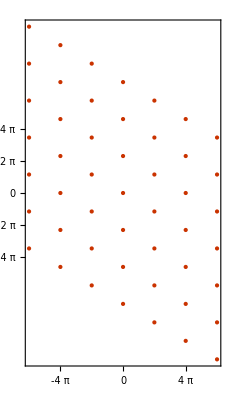

```mathematica
Block[{b1,b2,Gs,Q=4π},
b1={2π,-2π/Sqrt[3]};
b2={0,4π/Sqrt[3]};
Gs=Tuples[Range[-3,3],2].{b1,b2};
Graphics[{Red,Point[Gs]},PlotRange->Q,PlotRangePadding->Scaled[.02],PlotRangeClipping->True,Frame->True,FrameStyle->Black,FrameTicks->{{Range[-Q,Q,2π],None},{Range[-Q,Q,2π],None}},ImageSize->{Automatic,120}]]
```

Matching the previous numerical result by Fourier transform

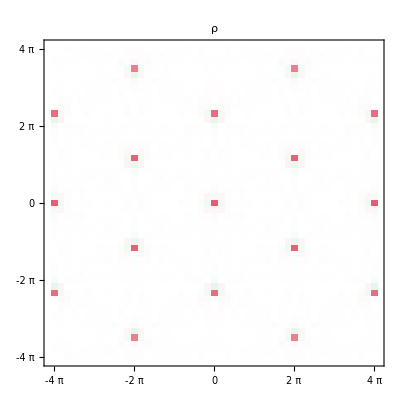

```mathematica
Block[{L=12,Q=4π,Rs,rs,qs},
Rs=Cases[Tuples[Range[-14,14],2].{{1,0},{1/2,Sqrt[3]/2}},p_/;Norm[p]<=L];
qs=N@Table[{qx,qy},{qy,Q,-Q,-2π/L},{qx,-Q,Q,2π/L}];
ComplexMatrixPlot[Total[Exp[ⅈ tTr[{qs,Rs},{{3,5}}]],{-1}]/Length[Rs],DataRange->{{-1,1},{-1,1}}Q,Frame->True,FrameStyle->Black,FrameTicks->{Range[-Q,Q,2π],Range[-Q,Q,2π]},PlotLabel->Style["\!\(ρ\&~(q)\)",14,Black],ImageSize->{Automatic,140}]]
```

Show that the body-centered cubic (BCC) lattice and the face-centered cubic (FCC) lattice are reciprocal lattices of each other. 
-Graphics3D--Graphics3D-

#### Brillouin Zone

Brillouin zone (BZ): a primitive unit cell of the reciprocal lattice.

The first Brillouin zone (1st BZ): the Wigner-Seitz cell centered at G=0 on the reciprocal lattice; also as the set of all points k in the momentum space, that are closest to G=0 than another points G on the reciprocal lattice.

The nth Brillouin zone: the set of all points k in the momentum space, that are nth closest to G=0 among another points G on the reciprocal lattice.

Examples of Brillouin zones (see [Reference] for the construction algorithm):

On 1D reciprocal lattice

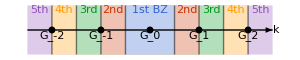

```mathematica
Block[{M=2,h=0.4},
Graphics[{{Table[Block[{col=ColorData[0][2m],BZ=<|1->"1st",2->"2nd",3->"3rd",4->"4th",5->"5th"|>[2m]},{{Lighter[col,0.7],Rectangle[{-m,-h},{m,h}]},{col,If[m==1/2,Text[BZ<>" BZ",{0,h},{0,1}],{Text[BZ,{m-1/4,h},{0,1}],Text[BZ,{-m+1/4,h},{0,1}]}]}}],{m,M+1/2,1/2,-1/2}]},
{Arrow[{#(M+0.5),0}&/@{-1,1}]},
{AbsolutePointSize[5],Table[Translate[{Point[{0,0}],Text[StringTemplate["\!\(G\_`1`\)"][m],{0,0},{0,1.2}]},{m,0}],{m,-M,M}]},
{AbsoluteThickness[1],Opacity[0.5],Table[If[m≠0,Translate[{Line[{0,# h}&/@{-1,1}]},{m,0}]],{m,-M,M,1/2}]},Text["\!\(k\)",{M+1/2,0},{-1.2,0}]},ImageSize->300]]
```

On 2D square reciprocal lattice

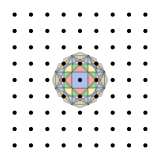

```mathematica
Block[{M=4,pts,k2p,polyreg,update},
pts=Tuples[Range[-M,M],2];
k2p=Block[{n2p=GroupBy[pts,Norm]},n2p/@AssociationThread[Range[0,Length[#]-1]->#&@SortBy[Keys@n2p,N]]];
polyreg[poly_]:=ReplaceRepeated[poly,{h:(Polygon|Triangle)[{pre___,p1_,p2_,post___}]/;Norm[p1-p2]<0.001:>Head[h][{pre,(p1+p2)/2,post}],h:(Polygon|Triangle)[{p1_,mid___,p2_}]/;Norm[p1-p2]<0.001:>Head[h][{(p1+p2)/2,mid}]}];
update[rank_,p_List]:=Block[{inner,outer,ins,mids,outs},
{inner,outer}=HalfPlane[(0.5-0.00001#)p,{{0,-1},{1,0}}.p,# p]&/@{-1,1};
{ins,mids,outs}=Flatten[{{Lookup[#,True,{}]},{Lookup[#,False,{}],Lookup[#,True,{}]}&@GroupBy[Lookup[#,False,{}],RegionWithin[outer,#]&]}&@GroupBy[Keys@rank,RegionWithin[inner,#]&],1];
Association[Join[Table[poly->rank[poly],{poly,ins}],Table[polyreg@RegionIntersection[poly,inner]->rank[poly],{poly,mids}],Table[polyreg@RegionIntersection[poly,outer]->rank[poly]+1,{poly,mids}],Table[poly->rank[poly]+1,{poly,outs}]]]];
update[rank_,k_Integer]:=Fold[update,rank,k2p@k];
Block[{rank},
rank=Fold[update,<|Polygon[CirclePoints[{1.7,0},8]]->1|>,Range[6]];
rank=Select[rank,#<=8&];
Graphics[{{EdgeForm[Directive[AbsoluteThickness[1],Opacity[0.2]]],Table[Block[{col={Blue,Red,Green,Yellow,Purple,Cyan,Orange,LightGreen}[[rank[poly]]]},{{Lighter[col,0.6],poly}(*,If[Area[poly]>=1/8,{col,Text[closerank[poly],RegionCentroid[poly]]}]*)}],{poly,Keys@rank}]},
{Point[pts]}},PlotRange->2,PlotRangePadding->0.2,ImageSize->160]
]]
```

On 2D triangular reciprocal lattice

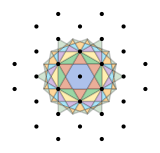

```mathematica
Block[{M=3,pts,k2p,polyreg,update},
pts=N@Cases[Tuples[Range[-M,M],2].{{Sqrt[3]/2,-1/2},{0,1}},p_/;Norm[p]<M];
k2p=Block[{n2p=GroupBy[pts,Norm]},n2p/@AssociationThread[Range[0,Length[#]-1]->#&@SortBy[Keys@n2p,N]]];
polyreg[poly_]:=ReplaceRepeated[poly,{h:(Polygon|Triangle)[{pre___,p1_,p2_,post___}]/;Norm[p1-p2]<0.001:>Head[h][{pre,(p1+p2)/2,post}],h:(Polygon|Triangle)[{p1_,mid___,p2_}]/;Norm[p1-p2]<0.001:>Head[h][{(p1+p2)/2,mid}]}];
update[rank_,p_List]:=Block[{inner,outer,ins,mids,outs},
{inner,outer}=HalfPlane[(0.5-0.00001#)p,{{0,-1},{1,0}}.p,# p]&/@{-1,1};
{ins,mids,outs}=Flatten[{{Lookup[#,True,{}]},{Lookup[#,False,{}],Lookup[#,True,{}]}&@GroupBy[Lookup[#,False,{}],RegionWithin[outer,#]&]}&@GroupBy[Keys@rank,RegionWithin[inner,#]&],1];
Association[Join[Table[poly->rank[poly],{poly,ins}],Table[polyreg@RegionIntersection[poly,inner]->rank[poly],{poly,mids}],Table[polyreg@RegionIntersection[poly,outer]->rank[poly]+1,{poly,mids}],Table[poly->rank[poly]+1,{poly,outs}]]]];
update[rank_,k_Integer]:=Fold[update,rank,k2p@k];
Block[{rank},
rank=Fold[update,<|Polygon[CirclePoints[{Sqrt[3],0},6]]->1|>,Range[4]];
rank=Select[rank,#<=8&];
Graphics[{{EdgeForm[Directive[AbsoluteThickness[1],Opacity[0.2]]],Table[Block[{col={Blue,Red,Green,Yellow,Purple,Cyan,Orange,LightGreen}[[rank[poly]]]},{{Lighter[col,0.6],poly}(*,If[Area[poly]>=1/8,{col,Text[closerank[poly],RegionCentroid[poly]]}]*)}],{poly,Keys@rank}]},
{Point[pts]}},PlotRange->2,PlotRangePadding->0.2,ImageSize->160]
]]
```

Properties:

The 1st BZ provides a compete set of inequivalent wave vectors. Any wave vector outside the 1st BZ will be equivalent to one inside the 1st BZ (related by certain lattice momentum).

Every BZ has exactly the same volume (in the momentum space):

det|B|=(2π)^n/(det|A|)=(2π)^n/Ω.

Higher BZ can be folded to the 1st BZ.

Any physical property (e.g. frequency, group velocity) of the wave propagating on a lattice can be fully described within the 1st BZ.

Smith, Philip. Geometric and Topological Methods for Applications to Materials and Data Skeletonisation. PhD thesis, University of Liverpool (2021).

### Scattering Experiment

#### Elastic Scattering

How do we probe the lattice structure? - Scattering experiment.

X-ray scattering.

Neutron scattering.

Electron scattering.

Note: Particles are waves. — Quantum Mechanics

##### Real Space Picture

Plane wave hits an atom, the atom responses with a spherical wave.

```mathematica
Block[{R=3,r=0.1,in,out,pts,plt},
in[{x_,y_}]:=Exp[2π ⅈ x];
out[{x_,y_}]:=HankelH1[0,2π Sqrt[x^2+y^2]];
pts={{0,0}};plt[fun_]:=Graphics[{Raster[Table[fun[{x,y}],{y,-R,R,0.1},{x,-R,R,0.1}],{{-R,-R},{R,R}},ColorFunction->ComplexColor],{EdgeForm[Directive[Black,AbsoluteThickness[1]]],{ComplexColor[fun[#+{r,0}]],Disk[#,r]}&/@pts}},ImageSize->90];
Style[Row[{plt[0.7in[#]&],"+",plt[-0.7Sum[in[pt]out[#-pt],{pt,pts}]&],"=",plt[0.7(in[#]-Sum[in[pt]out[#-pt],{pt,pts}])&]}],14,FontFamily->"LaTeX"]]
```

-Graphics-+-Graphics-=-Graphics-

Each atom behaves like an independent scatterer for the incident wave (to the leading order, ignoring the fact that the atoms can continue to scatter the wave that was scattered from other atoms).

```mathematica
Block[{R=3,r=0.1,in,out,pts,plt},
in[{x_,y_}]:=Exp[2π ⅈ x];
out[{x_,y_}]:=HankelH1[0,2π Sqrt[x^2+y^2]];
pts={{0,1},{0,-1}};plt[fun_]:=Graphics[{Raster[Table[fun[{x,y}],{y,-R,R,0.1},{x,-R,R,0.1}],{{-R,-R},{R,R}},ColorFunction->ComplexColor],{EdgeForm[Directive[Black,AbsoluteThickness[1]]],{ComplexColor[fun[#+{r,0}]],Disk[#,r]}&/@pts}},ImageSize->90];
Style[Row[{plt[0.7in[#]&],"+",plt[-0.7Sum[in[pt]out[#-pt],{pt,pts}]&],"=",plt[0.7(in[#]-Sum[in[pt]out[#-pt],{pt,pts}])&]}],14,FontFamily->"LaTeX"]]
```

-Graphics-+-Graphics-=-Graphics-

If there is an array of atoms, the scattering wave emitted from each atom can interfere → leading to Bragg diffraction.

```mathematica
Block[{R=3,r=0.1,in,out,pts,plt},
in[{x_,y_}]:=Exp[2π ⅈ x];
out[{x_,y_}]:=Exp[2π ⅈ Sqrt[x^2+y^2]]/((x^2+y^2)/r^2+1)^(1/4);
pts=Flatten[Table[{x,y},{y,-1,1},{x,-1,1}],1];plt[fun_]:=Graphics[{Raster[Table[fun[{x,y}],{y,-R,R,0.1},{x,-R,R,0.1}],{{-R,-R},{R,R}},ColorFunction->ComplexColor],{EdgeForm[Directive[Black,AbsoluteThickness[1]]],{ComplexColor[fun[#+{r,0}]],Disk[#,r]}&/@pts}},ImageSize->90];
Style[Row[{plt[0.5in[#]&],"+",plt[-0.5Sum[in[pt]out[#-pt],{pt,pts}]&],"=",plt[0.5(in[#]-Sum[in[pt]out[#-pt],{pt,pts}])&]}],14,FontFamily->"LaTeX"]]
```

-Graphics-+-Graphics-=-Graphics-

As we zoom out, the wave scattered off the crystal looks like beams of plane waves along special directions.

```mathematica
Manipulate[Block[{R=8,r=0.1,in,out,pts,plt},
in[{x_,y_}]:=Exp[2π ⅈ x];
out[{x_,y_}]:=Exp[2π ⅈ Sqrt[x^2+y^2]]/((x^2+y^2)/r^2+1)^(1/4);
pts=Flatten[Table[ReIm[(x+ⅈ y)Exp[ⅈ θ]],{y,-1,1},{x,-1,1}],1];plt[fun_]:=Graphics[{Raster[Table[fun[{x,y}],{y,-R,R,0.2},{x,-R,R,0.2}],{{-R,-R},{R,R}},ColorFunction->ComplexColor],{EdgeForm[Directive[Black,AbsoluteThickness[1]]],{ComplexColor[fun[#]],Disk[#,r]}&/@pts}},ImageSize->150];
Show[plt[-0.7Sum[in[pt]out[#-pt],{pt,pts}]&],Graphics[{Arrowheads[0.06],Arrow[{2#,7#}]&/@ReIm[Cases[1+(Tuples[Range[-2,2],{2}].{1,ⅈ})Exp[ⅈ θ],z_/;Abs[Abs[z]-1]<0.15]]}]]],{θ,0,π/2,ImageSize->Small},ContinuousAction->False,Paneled->False,SaveDefinitions->True]
```

Question: Why the scattering amplitude is strong along these directions? How to determine these directions?

##### Momentum Space Picture

Plane wave of wave momentum k (length of k - 2π/λ, direction of k - propagation direction)

ψ_k(r)=ⅇ^(ⅈ k·r).

Spherical wave = superposition of plane waves of the same wave length in all directions

ϕ_k(r)=∫_(|k|=k) ψ_k(r)=∫_(|k|=k) ⅇ^(ⅈ k·r)
=1/(2π)∫ⅆθ ⅇ^(ⅈ k r cos θ)=J_0(k r).

An atom scatters a plane wave of momentum k to a spherical wave of the same wave number k ⇔ to a equal-probability superposition of plane waves of all possible momentum k', as long as |k'|=|k|=k (the wave length does not change, as it is fixed by the wave frequency).

```mathematica
Graphics[{{Arrowheads[0.08],{Red,Arrow[{{-2,0},{-0.5,0}}],Text["\!\(k\)",{-2,0},{1.2,0}]},{Blue,Arrow[{0.5#,2#}]&/@CirclePoints[{1,π/12},12],Text["\!\(k\^′\)",{0,1.5}]}},{EdgeForm[AbsoluteThickness[1]],White,Disk[{0,0},0.1]}},ImageSize->100]
```

-Graphics-

Scattering rate Γ(k→k'): the probability (transition rate) to scatter a wave from momentum k to momentum k' by a set of scatterers of the density distribution ρ(r). According to Fermi’s golden rule,

Γ(k→k')∝(|k'ρk|)^2 δ(E_k'-E_k),

where

the scattering amplitude k'ρk is given by the wave function overlap

k'ρk=∫_r ψ_k'^*(r)ρ(r)ψ_k(r)
=∫_r ρ(r)ⅇ^(-ⅈ(k'-k)·r)
=ρ̃(k'-k)

ψ_k(r) - incident wave,

ρ(r) - scatterer density distribution (~ atomic density distribution),

ρ(r)ψ_k(r) - incident wave enveloped by the atomic density (no atom no scattering, more atom stronger scattering),

∫_r ψ_k'^*(r)… - inner product with ψ_k'(r) to extract the amplitude of wave in the k' momentum component.

The integration result can be expressed in terms of the Fourier transform of the density distribution

ρ̃(q)≡∫_r ρ(r)ⅇ^(-ⅈq·r).

the term δ(E_k'-E_k) imposes the energy conservation, which requires |k'|=|k| (the on-shell condition).

In conclusion, the scattering rate is given by

Γ(k→k')∝(|ρ̃(k'-k)|)^2 δ(E_k'-E_k).

Apply to a single atom at the origin: ρ(r)=δ(r),

ρ̃(q)=∫_r δ(r)ⅇ^(-ⅈq·r)=ⅇ^(-ⅈq·0)=1.

Therefore the scattering rate is constant for all k' as long as it is on-shell

Γ(k→k')∝δ(E_k'-E_k)∝δ(|k'|-|k|).

This matches the intuition that an atom scatters a plane wave to a spherical wave.

#### Fourier Transform of Lattice

Let us explore the behavior of the Fourier transform Eq. (DisplayFormulaNumbered).

ρ̃(q)≡∫_r ρ(r)ⅇ^(-ⅈq·r).

1D lattice R_n=n a,

Real-space density distribution (modeled by a sequence of Dirac peaks)

ρ(r)=1/N∑_(n∈ℤ) δ(r-R_n)=1/N∑_(n∈ℤ) δ(r-n a)

Momentum-space density distribution

ρ̃(q)=1/N∑_(n∈ℤ) ⅇ^(-ⅈ q R_n)=1/N∑_(n∈ℤ) ⅇ^(-ⅈ q n a)
=(2π)/(N a)∑_(m∈ℤ) δ(q-(2π m)/a)=(2π)/V∑_(m∈ℤ) δ(q-G_m).

Also a sequence of Dirac peaks located at reciprocal lattice sites:

G_m=(2π)/a m.

Argument: constructive interference from all lattice sites happens only when the wave length λ=a/m is an integer fraction of the lattice spacing a.

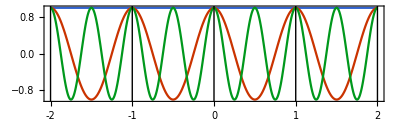

```mathematica
Plot[Evaluate@Table[Cos[2π r l],{l,0,2}],{r,-2,2},GridLines->{Range[-2,2],None},GridLinesStyle->Directive[Black, AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{Range[-2,2],{#,}&/@Range[-2,2]}},AspectRatio->0.3,FrameLabel->{"\!\(r/a\)",None},ImageSize->{Automatic,120}]
```

Show that in the functional sense
(i) ∑_(n∈ℤ) ⅇ^(-ⅈ n θ)=2π ∑_(m∈ℤ) δ(θ-2π m),
(ii) δ(q a)=1/a δ(q).

(i) Regularize the infinite sum by a finite sum

∑_(n=-(N-1)/2)^((N-1)/2) ⅇ^(-ⅈ n θ)=ⅇ^(ⅈ (N-1)/2 θ)∑_(n=0)^(N-1) ⅇ^(-ⅈ n θ)
=ⅇ^(ⅈ (N θ)/2)ⅇ^(-(ⅈ θ)/2)(1-ⅇ^(-ⅈ N θ))/(1-ⅇ^(-ⅈ θ))
=(ⅇ^(ⅈ (N θ)/2)-ⅇ^(-ⅈ (N θ)/2))/(ⅇ^((ⅈ θ)/2)-ⅇ^(-(ⅈ θ)/2))
=(sin (N θ)/2)/(sin θ/2).

For large N, the result is a series of peaks at θ=2π m, which is proportional to ∑_(m∈ℤ) δ(θ-2π m), with some proportionality constant c,

lim_(N→∞) (sin (N θ)/2)/(sin θ/2)=^functional c ∑_(m∈ℤ) δ(θ-2π m).

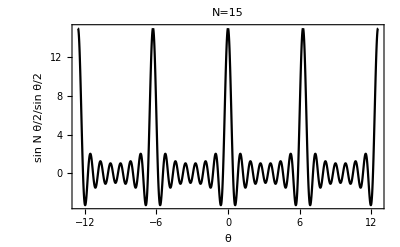

```mathematica
Block[{Ν=15},
Plot[Sin[Ν θ/2]/Sin[θ/2],{θ,-4π,4π},PlotStyle->Black,PlotRange->All,PlotLabel->Style[StringTemplate["\!\(N=`1`\)"][Ν],14,Black],FrameLabel->{"θ","\!\(\(sin N θ/2\)\/\(sin θ/2\)\)"},ImageSize->{Automatic,150}]]
```

To determine the constant c, we compare both sides of Eq. (DisplayFormulaNumbered) under integration of θ in [-π,π] (which extract the weight of a single peak).

∫_-π^π ⅆθ(sin (N θ)/2)/(sin θ/2)=2π,
∫_-π^π ⅆθ c∑_(m∈ℤ) δ(θ-2π m)=∫_-π^π ⅆθ c δ(θ)=c.

Therefore, c=2π is determined. Then Eq. (DisplayFormulaNumbered) can be written as

∑_(n∈ℤ) ⅇ^(-ⅈ n θ)=lim_(N→∞) ∑_(n=-(N-1)/2)^((N-1)/2) ⅇ^(-ⅈ n θ)=2π ∑_(m∈ℤ) δ(θ-2π m).

(ii) δ(q a) describes a peak at q=0, which should be proportional to δ(q), with some proportionality constant c

δ(q a)=c δ(q).

To determine the constant c, we compare both sides of Eq. (DisplayFormulaNumbered) under integration of q,

∫ⅆq δ(q a)=1/a∫ⅆ(q a) δ(q a)
=1/a∫ⅆx δ(x)
=1/a,
∫ⅆq c δ(q)=c.

Therefore c=1/a, such that δ(q a)=a^-1 δ(q).

Combining these results we can further show that

∑_(n∈ℤ) ⅇ^(-ⅈ q n a)=∑_(n∈ℤ) ⅇ^(-ⅈ n (q a))
=2π ∑_(m∈ℤ) δ(q a-2π m)
=2π ∑_(m∈ℤ) δ((q-(2π m)/a)a)
=(2π)/a∑_(m∈ℤ) δ(q-(2π m)/a).

2D lattices (numerical examples)

Square lattice → square lattice

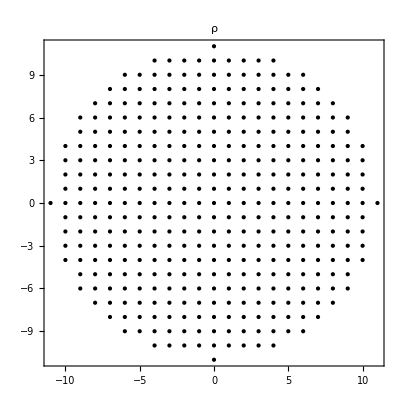
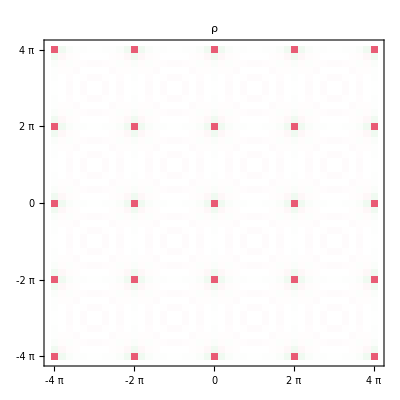

```mathematica
Block[{L=11,Q=4π,Rs,qs},
Rs=Cases[Tuples[Range[-12,12],2].{{1,0},{0,1}},p_/;Norm[p]<=L];
qs=N@Table[{qx,qy},{qy,Q,-Q,-2π/L},{qx,-Q,Q,2π/L}];
Row@{Graphics[{Black,Point[Rs]},PlotRange->2.5,PlotRangeClipping->True,Frame->True,PlotLabel->Style["\!\(ρ(r)\)",14,Black],ImageSize->{Automatic,140}],ComplexMatrixPlot[Total[Exp[ⅈ tTr[{qs,Rs},{{3,5}}]],{-1}]/Length[Rs],DataRange->{{-1,1},{-1,1}}Q,Frame->True,FrameStyle->Black,FrameTicks->{Range[-Q,Q,2π],Range[-Q,Q,2π]},PlotLabel->Style["\!\(ρ\&~(q)\)",14,Black],ImageSize->{Automatic,140}]}]
```

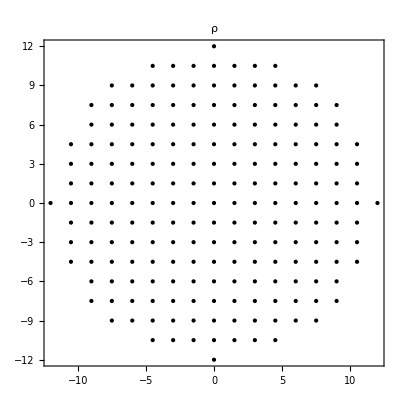
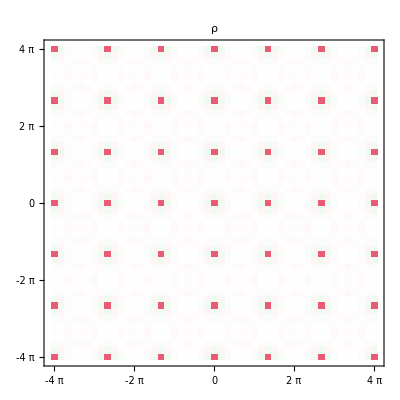

```mathematica
Block[{L=12,Q=4π,Rs,qs},
Rs=Cases[Tuples[Range[-12,12],2].{{1.5,0},{0,1.5}},p_/;Norm[p]<=L];
qs=N@Table[{qx,qy},{qy,Q,-Q,-2π/L},{qx,-Q,Q,2π/L}];
Row@{Graphics[{Black,Point[Rs]},PlotRange->2.5,PlotRangeClipping->True,Frame->True,PlotLabel->Style["\!\(ρ(r)\)",14,Black],ImageSize->{Automatic,140}],ComplexMatrixPlot[Total[Exp[ⅈ tTr[{qs,Rs},{{3,5}}]],{-1}]/Length[Rs],DataRange->{{-1,1},{-1,1}}Q,Frame->True,FrameStyle->Black,FrameTicks->{Range[-Q,Q,2π],Range[-Q,Q,2π]},PlotLabel->Style["\!\(ρ\&~(q)\)",14,Black],ImageSize->{Automatic,140}]}]
```

Direct lattice expands in the real space ⇔ reciprocal lattice shrinks in the momentum space (hence the name “reciprocal”). Reason: momentum and coordinate scales are reciprocal to each other (q∼a^-1).

Triangular lattice → triangular lattice

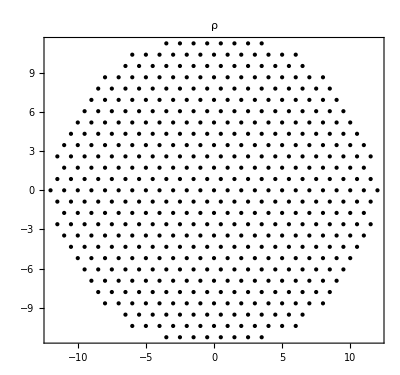
-Graphics--Graphics-

```mathematica
Block[{L=12,Q=4π,Rs,rs,qs},
Rs=Cases[Tuples[Range[-14,14],2].{{1,0},{1/2,Sqrt[3]/2}},p_/;Norm[p]<=L];
qs=N@Table[{qx,qy},{qy,Q,-Q,-2π/L},{qx,-Q,Q,2π/L}];
Row@{Graphics[{Point[Rs]},PlotRange->2.2,PlotRangeClipping->True,Frame->True,PlotLabel->Style["\!\(ρ(r)\)",14,Black],ImageSize->{Automatic,140}],ComplexMatrixPlot[Total[Exp[ⅈ tTr[{qs,Rs},{{3,5}}]],{-1}]/Length[Rs],DataRange->{{-1,1},{-1,1}}Q,Frame->True,FrameStyle->Black,FrameTicks->{Range[-Q,Q,2π],Range[-Q,Q,2π]},PlotLabel->Style["\!\(ρ\&~(q)\)",14,Black],ImageSize->{Automatic,140}]}]
```

Reciprocal lattice shares the same point group symmetry as the direct lattice. (In this case, six-fold rotation, horizontal and vertical reflections).

Honeycomb lattice (triangular Bravais lattice + sub-lattice structure) → triangular lattice with non-trivial structure factor.

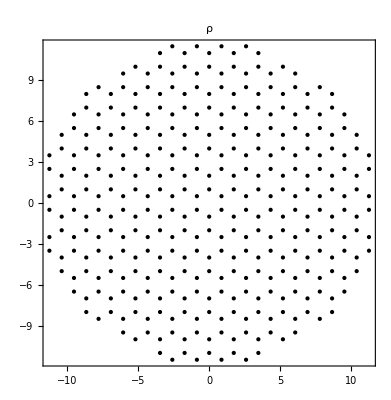
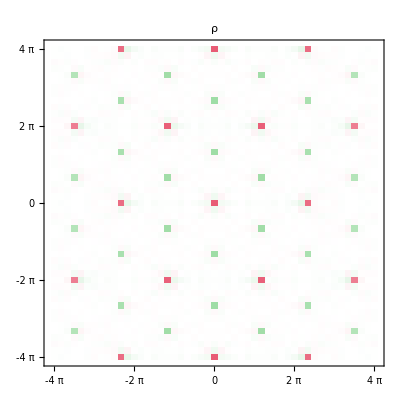

```mathematica
Block[{L=12,Q=4π,Rs,qs},
Rs=Cases[Join@@Table[(#+r)&/@#,{r,{{Sqrt[3],1},{Sqrt[3],1}/2}}]&[Tuples[Range[-14,14],2].{{Sqrt[3],0},{Sqrt[3]/2,3/2}}],p_/;Norm[p]<=L];
qs=N@Table[{qx,qy},{qy,Q,-Q,-2π/L},{qx,-Q,Q,2π/L}];
Row@{Graphics[{Point[Rs]},PlotRange->2.9,PlotRangeClipping->True,Frame->True,PlotLabel->Style["\!\(ρ(r)\)",14,Black],ImageSize->{Automatic,140}],ComplexMatrixPlot[Total[Exp[ⅈ tTr[{qs,Rs},{{3,5}}]],{-1}]/Length[Rs],DataRange->{{-1,1},{-1,1}}Q,Frame->True,FrameStyle->Black,FrameTicks->{Range[-Q,Q,2π],Range[-Q,Q,2π]},PlotLabel->Style["\!\(ρ\&~(q)\)",14,Black],ImageSize->{Automatic,140}]}]
```

red dot - positive peak, green dot - negative peak. Non-trivial sub-lattice structure leads to non-trivial structure factor (To be discussed in more details).

In general, for atoms at R_(n,s) on a lattice, the scatterer density distribution can be modeled by

ρ(r)=1/N∑_(n,s) f_s δ(r-R_(n,s)),

where

f_s is the scattering amplitude of the type-s atom (different types of atom can scatter the wave with different amplitudes). Normalization: ∑_s f_s=1.

N - number of unit cells. Assume thermodynamic limit N->∞. The average  1/N∑_R … has a well-defined limit as N→∞. The normalization condition is ∫_r ρ(r)=1.

Therefore by Eq. (DisplayFormulaNumbered),

ρ̃(q)=∫_r ρ(r)ⅇ^(-ⅈq·r)
=1/N∫_r ∑_(n,s) f_s δ(r-R_(n,s))ⅇ^(-ⅈq·r)
=1/N∑_(n,s) f_s ⅇ^(-ⅈ q·R_(n,s)).

Given R_(n,s)=R_n+r_s (recall Eq. (DisplayFormulaNumbered)), the summation can be split into two parts

ρ̃(q)=1/N∑_n ⅇ^(-ⅈ q·R_n)∑_s f_s ⅇ^(-ⅈ q·r_s).

If the lattice is a Bravais lattice, there is only one type of atom (no sub-lattice structure), the second summation is just a trivial factor f, which may be rescaled to f=1, such that the scattering amplitude ρ̃(q) is given by the Fourier series

ρ̃(q)=1/N∑_n ⅇ^(-ⅈ q·R_n).

Expect ρ̃(q) to peak at multiple points arranged periodically in the momentum space, forming the reciprocal lattice.

#### Scattering Amplitude

Recall that the scattering rate is given by Eq. (DisplayFormulaNumbered),

Γ(k→k')∝(|ρ̃(k'-k)|)^2 δ(E_k'-E_k),

where the scattering amplitude is (recall Eq. (DisplayFormulaNumbered))

ρ̃(q)=1/N∑_n ⅇ^(-ⅈ q·R_n)∑_s f_s ⅇ^(-ⅈ q·r_s).

Given the knowledge of reciprocal lattice, the first summation can be evaluated as (use (Exc. Exercise) results and generalize to higher dimensions)

∑_n ⅇ^(-ⅈ q·R_n)=(2π)^D/Ω∑_m δ(q-G_m),

D - space dimension.

Ω - unit cell volume, as defined in Eq. (DisplayFormulaNumbered).

G_m - reciprocal lattice vectors, as in Eq. (DisplayFormulaNumbered), labeled by Miller indices m.

If q is a reciprocal lattice point, ⅇ^(-ⅈ q·R_n) will be unity and the sum is infinite, however if q is not on the reciprocal lattice, the sum will be zero due to the phase cancellation of ⅇ^(-ⅈ q·R_n). Such behavior is exactly described by the delta function on the right-hand-side.

Then Eq. (DisplayFormulaNumbered) can be written as (note N Ω=V is the total volume)

ρ̃(q)=(2π)^D/V∑_m δ(q-G_m)∑_s f_s ⅇ^(-ⅈ q·r_s)
=(2π)^D/V∑_m δ(q-G_m)∑_s f_s ⅇ^(-ⅈ G_m·r_s)

where we are free to replace q by G_m because ρ̃(q) is non-vanishing only when q=G_m (when the replacement is valid).

In summary, the scattering amplitude takes the form of

ρ̃(q)=(2π)^D/V∑_m S_m δ(q-G_m),
S_m=∑_s f_s ⅇ^(-ⅈ G_m·r_s).

such that ρ̃(q) contains

a collection of peaks at q=G_m described by δ(q-G_m),

whose amplitude is given by the structural factor S_m (it is determined by the sub-lattice structure, and appears as a factor in front of the delta function peak, hence the name).

The direct lattice (atomic density distribution ρ(r)) can be restored from the scattering amplitude ρ̃(q) by the inverse Fourier transform

ρ(r)≡1/(2π)^D∫_q ρ̃(q)ⅇ^(ⅈ q·r).

Therefore the result of scattering experiment can be used to infer the lattice structure.

Show that Eq. (DisplayFormulaNumbered) indeed restores Eq. (DisplayFormulaNumbered) given Eq. (DisplayFormulaNumbered).

Substitute Eq. (DisplayFormulaNumbered) into Eq. (DisplayFormulaNumbered),

ρ(r)=1/(2π)^D∫_q ρ̃(q)ⅇ^(ⅈ q·r)
=1/V∫_q ∑_m S_m δ(q-G_m)ⅇ^(ⅈ q·r)
=1/V∑_m S_m ⅇ^(ⅈ G_m·r)
=1/V∑_m ∑_s f_s ⅇ^(-ⅈ G_m·r_s)ⅇ^(ⅈ G_m·r)
=1/V∑_s f_s∑_m ⅇ^(ⅈ G_m·(r-r_s)).

Similar to Eq. (DisplayFormulaNumbered), for the inverse Fourier series, we have

∑_m ⅇ^(ⅈ G_m·r)=Ω∑_n δ(r-R_n),

therefore Eq. (DisplayFormulaNumbered) becomes

ρ(r)=Ω/V∑_s f_s∑_n δ(r-r_s-R_n)
=1/N∑_(n,s) f_s δ(r-R_(n,s)).

#### Laue Condition

The scattering rate Γ(k→k') peaks (i.e. the scattering happens) when the following conditions are met

conservation of crystal momentum (Laue condition)

k'-k=G_m,

conservation of energy (for X-ray E_k=c ℏ|k|, for neutron / electron E_k=ℏ^2/(2m)(|k|)^2)

|k'|=|k|.

Graphical method to determine k' (scattered wave, in blue) from k (incident wave, in red) given the reciprocal lattice.

```mathematica
Manipulate[Block[{b1,b2,Gs,Q=4π},
b1={0,2π};
b2={-2π,0};
Gs=Tuples[Range[-5,5],2].{b1,b2};
Graphics[{{Purple,Circle[{0,0},k]},{Arrowheads[0.06],Red,Arrow[ReIm@{0,k}],Blue,Arrow[ReIm@{0,#}]&/@Cases[k+Exp[ⅈ θ]Gs.{1,ⅈ},z_/;Abs[Abs[z]-k]<0.2&&Abs[z-k]>0.01]},{AbsolutePointSize[5],Point[ReIm[k+Exp[ⅈ θ]Gs.{1,ⅈ}]]}},
PlotRange->Q,PlotRangePadding->Scaled[.02],PlotRangeClipping->True,Frame->True,FrameStyle->Black,FrameTicks->{{Range[-Q,Q,2π],None},{Range[-Q,Q,2π],None}},ImageSize->{Automatic,140}]],
{{k,2π},0,4π,ImageSize->Small},{θ,0,π/2,ImageSize->Small},Paneled->False,SaveDefinitions->True]
```

k - wave number 2π/λ,

θ - rotation angle of the crystal (reciprocal lattice rotates by the same amount as the direct lattice).

#### Lattice Momentum

What is the physical meaning of the lattice momentum ℏG?

Lattice (Bravais lattice) = the intersection of families of lattice planes of all lattice momenta G

ρ(r)=1/N∑_n δ(r-R_n)=1/V∑_m ⅇ^(ⅈ G_m·r),

see (Exc. Exercise) for derivation.

Take the triangular lattice for example:

```mathematica
Block[{L=2.2,Rs,b1,b2,plt,ms},
Rs=Cases[Tuples[Range[-3,3],2].{{1,0},{1/2,Sqrt[3]/2}},{x_,y_}/;Abs[x]<=2&&Abs[y]<=2];
b1={0,4π/Sqrt[3]};
b2={-2π,2π/Sqrt[3]};
plt[fun_]:=Graphics[{Raster[Table[fun[{x,y}],{y,-L,L,0.1},{x,-L,L,0.1}],{{-L,-L},{L,L}},ColorFunction->ComplexColor],
{AbsoluteThickness[1],Circle[#,Offset@{2,2}]&/@Rs}},BaselinePosition->(Axis->Baseline),ImageSize->70];
ms={{1,0},{0,1},{1,-1}};
Style[Row[{Row[Table[Show[{plt[Cos[m.{b1,b2}.#]&],Graphics[{Arrowheads[0.12],Arrow[{0.1#,1#}&@Normalize[m.{b1,b2}]]}]},PlotLabel->Style[StringTemplate["\!\(|G\_(`1`)⟩\)"][Row[m,","]],14,Black]],{m,ms}],"+"],"=",plt[Sum[Cos[m.{b1,b2}.#],{m,ms}]/Sqrt[3]&]}],14,FontFamily->"LaTeX"]
]
```

++-Graphics--Graphics--Graphics-=-Graphics-

Each family of lattice planes is in one-to-one correspondence with the possible directions of reciprocal lattice vectors G, to which they are normal.

The length of G is always an integer multiple of 2π/d,

|G|=(2π m)/d,

where d is the spacing between the lattice planes. (The corresponding wave length λ=d/m).

The particle that carries the momentum ℏ G is the condensed phonon in the crystal (To be explained later).

#### Bragg Condition

Laue condition can also be interpreted as the scattering condition associated with a diffraction grating.

An incoming wave is reflected off of a family of adjacent layers of atoms separated by the inter-layer distance d.

```mathematica
Block[{θ=π/3,R=2.5},Row[{Graphics[{Table[{{AbsoluteThickness[1],Dashing[0.04],Gray,Line[{{-2,y},{2,y}}]},{Arrowheads[{{0.01,0.8,Graphics[Line[Offset/@{{-5,-3},{0,0},{-5,3}}]]}}],Arrow[{{-R Cos[θ],R Sin[θ]}+y Cos[θ]{Sin[θ],Cos[θ]},{0,y}}],Arrow[{{0,y},{R Cos[θ],R Sin[θ]}+y Cos[θ]{-Sin[θ],Cos[θ]}}]},{AbsolutePointSize[5],Point[Table[{x,y},{x,-2,2}]]}},{y,0,-2,-1}],
Translate[{AbsoluteThickness[1],Arrowheads[{-0.06,0.06}],Arrow[{0,#}&/@{0,-1}],Text["\!\(d\)",{0,-0.5},{-1,0}]},{-1.8,-1}],
Translate[{AbsoluteThickness[1],{Dashing[{0.02,0.02}],Line[{{0,0},2Cos[θ]{Sin[θ],-Cos[θ]}}],Line[{{0,-1},Cos[θ]{Sin[θ],-Cos[θ]}+{0,-1}}]},
Translate[{Rotate[Line[Offset/@{{-4,0},{-4,4},{0,4}}],θ,{0,0}]},Cos[θ]{Sin[θ],-Cos[θ]}],Translate[{Arrowheads[{-0.06,0.06}],Arrow[{{0,0},Sin[θ]{Cos[θ],Sin[θ]}}],Text["\!\(d sin θ\)",Sin[θ]/2{Cos[θ],Sin[θ]},{-1.2,0}]},0.5Cos[θ]{Sin[θ],-Cos[θ]}+{0,-1}]},{0,-1}],
Translate[{AbsoluteThickness[1],Circle[{0,0},0.3,{π-θ,π}],Text["θ",ReIm[0.3 Exp[ⅈ (π-θ/2)]],{1,0}]},{0,-2}]},ImageSize->120],
Graphics[{{Arrowheads[0.4],Arrow[{{0,0},{Cos[θ],-Sin[θ]}}],Arrow[{{0,0},{Cos[θ],Sin[θ]}}],Arrow[{{Cos[θ],-Sin[θ]},{Cos[θ],Sin[θ]}}]},
{AbsoluteThickness[1],{Dashed,Line[{{0,0},{Cos[θ],0}}]},Circle[{0,0},0.2,{0,θ}],Text["θ",{0.3,0.15}]},
{Text["\!\(k\)",{Cos[θ],-Sin[θ]}/2,{1,1}],
Text["\!\(k\^′\)",{Cos[θ],Sin[θ]}/2,{0.2,-1}],
Text["\!\(G\)",{Cos[θ],0},{-1,0}]}},ImageSize->36]},Spacer[10]]]
```

-Graphics--Graphics-

The wave has been deflected by angle 2θ.

Wave deflected from the next deeper layer travels additional distance 2d sin θ (extra d sin θ accumulated on both the incoming and outgoing rays), compare to that from the previous layer.

Condition for constructive interference (Bragg condition)

2 d sin θ=m λ,

with m∈ℤ.

Bragg condition and Laue condition are equivalent.

2 d sin θ=m λ⇔k'-k=G.

Direction: the direction of k'-k is always normal to the lattice plane, matching the direction of G.

Length: |k'|=|k|=2π/λ, |G|=2π m/d.

2(2π)/λ sin θ=(2π m)/d⇒2d sin θ=m λ.

#### Structural Factor

The Bragg/Laue condition determines the positions of diffraction peaks (at G_m, labeled by Miller indices m), the intensity (|S_m|)^2 of each peak m is determined by the structural factor S_m (recall Eq. (DisplayFormulaNumbered))

S_m=∑_s f_s ⅇ^(-ⅈ G_m·r_s),

where

f_s is the atomic form factor (scattering amplitude) of the type-s atom,

r_s is the sub-lattice vector of the type-s atom.

It is sometimes more convenient to represent the sub-lattice vector r_s in the primitive lattice vector basis, by introducing n_s=(n_(s,1),n_(s,2),…),

r_s=∑_(i=1)^D n_(s,i)a_i.

Given that G_m=∑_(i=1)^D m_i b_i, Eq. (DisplayFormulaNumbered) can be written as

S_m=∑_s f_s exp(-ⅈ ∑_(i=1)^D m_i b_i·∑_(j=1)^D n_(s,j)a_j)
=∑_s f_s exp(-ⅈ ∑_(i,j) m_i n_(s,j)b_i·a_j)
=∑_s f_s exp(-2π ⅈ ∑_(i,j) m_i n_(s,j)i,j)
=∑_s f_s exp(-2π ⅈ ∑_i m_i n_(s,i)),

or in terms of a dot product

S_m=∑_s f_s ⅇ^(-2πⅈ m·n_s).

Examples:

Honeycomb lattice (recall Eq. (DisplayFormulaNumbered))

{ | a_1=(√3,0)
a_2=((√3)/2,3/2),{ | r_A=(√3,1)
r_B=((√3)/2,1/2).

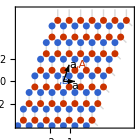

```mathematica
Block[{L=1,a1,a2,Rs},
a1={Sqrt[3],0};
a2={Sqrt[3],3}/2;
Rs=Tuples[Range[-L-2,L+2],2].{a1,a2};
Graphics[{{LightGray,AbsoluteThickness[1],Translate[Line[{{0,0},#}]&/@CirclePoints[{1,π/2},3],#+{Sqrt[3],1}]&/@Rs},{AbsolutePointSize[5],Blue,Point[#+{Sqrt[3]/2,1/2}&/@Rs],Red,Point[#+{Sqrt[3],1}&/@Rs]},{Arrowheads[0.06],{Arrow[{{0,0},#1}],Text[StringTemplate["\!\(\*StyleBox[\"a\",Bold]\_`1`\)"][#2],#1,#3]}&@@@{{a1,"1",{0,0.8}},{a2,"2",{-1.,-0.2}}}},
{Blue,Text["\!\(,B\)",{Sqrt[3]/2,1/2},{1.5,0.5}],Red,Text["\!\(,A\)",{Sqrt[3],1},{-1.5,-0.5}]}},PlotRange->2L,PlotRangeClipping->True,PlotRangePadding->0.8,Frame->True,FrameTicks->{{Range[-2L,2L],{#,""}&/@Range[-2L,2L]},{Range[-2L,2L],{#,""}&/@Range[-2L,2L]}},ImagePadding->{{Automatic, 5}, {Automatic, 5}},ImageSize->140]]
```

Rewrite r_s to n_s by Eq. (DisplayFormulaNumbered),

{ | n_A=(2/3,2/3)
n_B=(1/3,1/3).

The structure factor is given by Eq. (DisplayFormulaNumbered)

S_m=f_A ⅇ^(-2π ⅈ 2(m_1+m_2)/3)+f_B ⅇ^(-2π ⅈ (m_1+m_2)/3)
=f_A ϖ^(m_1+m_2)+f_B ϖ^(-(m_1+m_2)).

where ϖ=ⅇ^(2π ⅈ/3) is the third root of unity.

If f_A=f_B=f (A, B sub-lattices are equivalent as in graphene)

S_m=Piecewise[{{2f, m_1+m_2=^(mod 3)0}, {-f, m_1+m_2=^(mod 3)1,2}}].

The reciprocal lattice is given by G_m=m_1 b_1+m_2 b_2 with

{ | b_1=((2π)/(√3),-(2π)/3)
b_2=(0,(4π)/3).

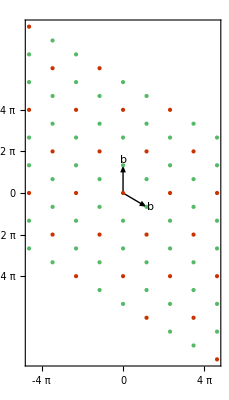

```mathematica
Block[{b1,b2,Q=4π},
b1={2π/Sqrt[3],-2π/3};
b2={0,4π/3};
Graphics[{{Arrowheads[0.1],Arrow[{{0,0},#}]&/@{b1,b2}},{Text["\!\(b\_"<>#1<>"\)",##2]&@@@{{"1",b1,{-1.2,0.3}},{"2",b2,{0,-0.7}}}},{If[Mod[#1+#2,3]==0,Red,Lighter[Green]],Point[#1 b1+#2 b2]}&@@@Tuples[Range[-4,4],2]},PlotRange->Q,PlotRangePadding->Scaled[.02],PlotRangeClipping->True,Frame->True,FrameStyle->Black,FrameTicks->{{Range[-Q,Q,2π],None},{Range[-Q,Q,2π],None}},ImageSize->{Automatic,120}]]
```

red - m_1+m_2=^(mod 3)0 ⇒ S_m=2f,

light green - m_1+m_2=^(mod 3)1,2 ⇒ S_m=-f.

Matching the numerical result of lattice Fourier transform.

```mathematica
Block[{L=12,Q=4π,Rs,qs},
Rs=Cases[Join@@Table[(#+r)&/@#,{r,{{Sqrt[3],1},{Sqrt[3],1}/2}}]&[Tuples[Range[-14,14],2].{{Sqrt[3],0},{Sqrt[3]/2,3/2}}],p_/;Norm[p]<=L];
qs=N@Table[{qx,qy},{qy,Q,-Q,-2π/L},{qx,-Q,Q,2π/L}];
ComplexMatrixPlot[Total[Exp[ⅈ tTr[{qs,Rs},{{3,5}}]],{-1}]/Length[Rs],DataRange->{{-1,1},{-1,1}}Q,Frame->True,FrameStyle->Black,FrameTicks->{Range[-Q,Q,2π],Range[-Q,Q,2π]},PlotLabel->Style["\!\(ρ\&~(q)\)",14,Black],ImageSize->{Automatic,140}]]
```

-Graphics-

Cubic lattice (recall Eq. (DisplayFormulaNumbered)) with both corner (A) and center (B) sites

{ | a_1=(1,0,0)
a_2=(0,1,0)
a_3=(0,0,1), { | r_A=(0,0,0)
r_B=(1/2,1/2,1/2).

```mathematica
Block[{pts},
pts={{0,0,0},{1,0,0},{0,1,0},{1,1,0},{0,0,1},{1,0,1},{0,1,1},{1,1,1},{1,1,1}/2};
Graphics3D[{GraphicsComplex[pts,
{{Red,Sphere[#,0.08]&/@Range[8],Text["\!\(A\)",2,{-1,1}]},{Blue,Sphere[9,0.08],Text["\!\(B\)",9,{0,-1}]},{Black,Tube[{{1,2,4,3,1},{5,6,8,7,5},{1,5},{2,6},{3,7},{4,8}}]},{LightGray,Tube[{9,#}&/@Range[8]]},{Black,Arrowheads[{{0.1,0.95}}],Arrow[Tube[{1,#},0.02]]&/@{2,3,5}},{Text[StringTemplate["\!\(\*StyleBox[\"a\",Bold]\_`1`\)"][#2],#1,#3]&@@@{{2,1,{1,-1}},{3,2,{1,-1}},{5,3,{-1.5,1}}}}}]},Lighting->"Neutral",ViewPoint->{2,0,1},Boxed->False,ImageSize->120]]
```

-Graphics3D-

Rewrite r_s to n_s by Eq. (DisplayFormulaNumbered),

{ | n_A=(0,0,0)
n_B=(1/2,1/2,1/2).

The structure factor is given by Eq. (DisplayFormulaNumbered)

S_m=f_A+f_B ⅇ^(-2π ⅈ (m_1+m_2+m_3)/2)
=f_A+(f_B(-1))^(m_1+m_2+m_3).

If f_A=f_B=f (A, B sub-lattices are equivalent as in body-centered cubic (BCC) lattice)

S_m=Piecewise[{{2f, m_1+m_2+m_3 is even}, {0, m_1+m_2+m_3 is odd}}].

The reciprocal lattice is given by G_m=∑_(i=1)^3 m_i b_i with

{ | b_1=2π (1,0,0)
b_2=2π (0,1,0)
b_3=2π (0,0,1).

```mathematica
Block[{b1,b2,b3},
{b1,b2,b3}=2π IdentityMatrix[3];
Graphics3D[{Table[{If[EvenQ[m1+m2+m3],Black,Opacity[0.5]],Sphere[m1 b1+m2 b2+m3 b3,0.5]},{m1,0,2},{m2,0,2},{m3,0,2}],
{Black,Rotate[Translate[Translate[Tube[{{0,0,0},2b1},0.05],# b2]&/@Range[0,2],# b3]&/@Range[0,2],2π #/3,{1,1,1},{0,0,0}]&/@Range[3]}},Lighting->"Neutral",ViewPoint->{3,-1,1},Boxed->False,ImageSize->140]]
```

-Graphics3D-

Solid (black) - m_1+m_2+m_3 even ⇒ S_m≠0. They form a face-centered cubic (FCC) lattice, verifying the fact that the reciprocal lattice of BCC lattice is a FCC lattice (see (HW Homework)).

Transparent - m_1+m_2+m_3 odd ⇒ S_m=0. These are called extinction points in the diffraction pattern, where the scattering wave is systematically absent.

Symmetry reason for the extinction phenomenon

When A, B sites are equivalent, the lattice symmetry is enlarged. For example, translation by the vector r_B=(1/2,1/2,1/2) becomes a symmetry (which was not for a simple cubic lattice). This means

ρ(r)=ρ(r+r_B),

is a new property of the density distribution ρ.

Under the symmetry action, the scattering amplitude ρ̃(q) transforms as (according to Eq. (DisplayFormulaNumbered))

ρ̃(q)=∫_r ρ(r)ⅇ^(-ⅈq·r)
→∫_r ρ(r+r_B)ⅇ^(-ⅈq·(r+r_B))
=ⅇ^(-ⅈq·r_B)∫_r ρ(r)ⅇ^(-ⅈq·r)
=ⅇ^(-ⅈq·r_B)ρ̃(q).

Apply to the reciprocal lattice points

ρ̃(G_m)→ⅇ^(-ⅈG_m·r_B)ρ̃(G_m)
=ⅇ^(-2π ⅈ m·n_B)ρ̃(G_m)
=(-1)^(m_1+m_2+m_3)ρ̃(G_m).

Therefore, if m_1+m_2+m_3 is odd, Eq. (DisplayFormulaNumbered) implies that ρ̃(G_m) will transform to -ρ̃(G_m). The only way to preserve ρ̃(G_m) under the symmetry transformation is to set ρ̃(G_m)=0, hence the extinction phenomenon.

### Summary

Relation between lattice and reciprocal lattice.

Bravais lattice |   | Reciprocal lattice
R_n=∑_(i=1)^D n_i a_i | ⇋_(b_i·a_j=2π δ_(i,j)) | G_m=∑_(i=1)^D m_i b_i
↓^(sub-lattice) |   |  
R_(n,s)=R_n+r_s |   |  
General lattice |   |

Volume of primitive unit cell

Ω=|a_1·(a_2×a_3)|.

Construct b_i from a_i

b_i=(2π)/Ω 1/2 ϵ_(i,j,k) a_j×a_k.

Fourier transformation between atomic density distribution ρ(r) and scattering amplitude ρ̃(q)

ρ(r)=1/N∑_(n,s) f_s δ(r-R_(n,s)) | ⇌_(ρ(r)=1/(2π)^D∫_q ρ̃(q)ⅇ^(ⅈ q·r))^(ρ̃(q)=∫_r ρ(r)ⅇ^(-ⅈq·r)) | ρ̃(q)=(2π)^D/V∑_m S_m δ(q-G_m)
   |   | (S_m=∑_s f_s ⅇ^(-ⅈ G_m·r_s))

ρ̃(q) determines the scattering rate

Γ(k→k')∝(|ρ̃(k'-k)|)^2 δ(E_k'-E_k).

Diffraction spot location is determined by either the Laue condition or the Bragg condition (they are equivalent)

{ | k'-k=G_m
|k'|=|k|⇔2 d sin θ=m λ.

Diffraction spot intensity (|S_m|)^2  is determined by the structural factor

S_m=∑_s f_s ⅇ^(-2πⅈ m·n_s).

Diffraction spot can extinct when S_m=0.

## Phonon

### Lattice Vibration

#### Hamiltonian of Atoms

The dynamics of a system of atoms is described by the Hamiltonian (kinetic energy + potential energy)

H=∑_i p_i^2/(2 m_i)+V(r_1,r_2,…),

where

p_i - the momentum of the ith atom,

r_i - the position of the ith atom,

m_i - the mass of the ith atom.

The total potential energy of atoms may be well modeled by pairwise inter-atomic interactions (recall Eq. (DisplayFormulaNumbered))

V(r_1,r_2,…)=∑_(i≠j) V(r_i-r_j),

where V(r) generally takes the following shape (short-range repulsion + longer range attraction):

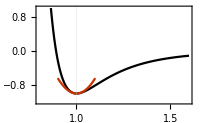

```mathematica
Show[Plot[1/r^12-2/r^6,{r,0.8,1.6},PlotStyle->Black,PlotRange->{-1.2,1.},FrameLabel->{"\!\(r/a\)","\!\(V(r)/V\_0\)"},GridLines->{{1},None},ImageSize->200],Plot[-1+36(r-1)^2,{r,0.9,1.1},PlotStyle->Red]]
```

At low energy (low temperature), the atoms are expected to form a crystal (that minimizes the potential energy) and oscillate around their equilibrium positions (around the potential minimum). Suppose the oscillation amplitude is small (otherwise the crystal may melt), the inter-atomic potential energy can be approximated by its 2nd order expansion around the minimum

V(r)=V_0+κ/2(r-a)^2+…,

where κ=∂_r^2 (V(r))_(r=a), as shown in the above figure as the red parabola.

#### Harmonic Approximation

This idea can be formulated more systematically:

Let R_i be the equilibrium position of the ith atom, and x_i be the displacement of the ith atom from its equilibrium position, s.t.

r_i=R_i+x_i.

Assuming x_i are small, expand the potential energy to the 2nd order of x_i

V(r_1,r_2,…)=V(R_1+x_1,R_2+x_2,…)
=V(R_1,R_2,…)
+∑_i x_i·∇_R_i V(R_1,R_2,…)
+1/2∑_(i,j) (x_i·∇_R_i)(x_j·∇_R_j)V(R_1,R_2,…)
+…

where

The 0th order term V(R_1,R_2,…)=V_eq is a constant shift of energy, which can be dropped from the Hamiltonian without affecting dynamics.

The 1st order term vanishes, because the gradient ∇_R_i V=0 vanishes at equilibrium (by definition).

The 2nd order term takes the form of

1/2∑_(i,j) x_i·K_(i,j)·x_j,

where K_(i,j) is a matrix for every i,j, and is called the elastic tensor,

K_(i,j)=∇_R_i ∇_R_j V(R_1,R_2,…).

Thus the Hamiltonian in Eq. (DisplayFormulaNumbered) can be approximated by

H=∑_i p_i^2/(2 m_i)+1/2∑_(i,j) x_i·K_(i,j)·x_j.

It describes a set of coupled harmonic oscillators, which models the lattice vibration.

Apply to the pairwise interaction model Eq. (DisplayFormulaNumbered), and assume the inter-atomic interaction V(r)=V(r) is isotropic, by Taylor expansion,

1/2∑_(i,j) x_i·K_(i,j)·x_j=1/2∑_(i≠j) ((κ_(i,j)^⊥(x_i-x_j))^2+(κ_(i,j)^∥-κ_(i,j)^⊥)((R̂)_(i,j)·(x_i-x_j))^2 ),

where

(R̂)_(i,j)=R_(i,j)/|R_(i,j)| is the unit vector along the bond displacement R_(i,j)=R_i-R_j,

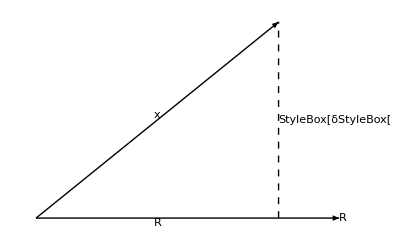

```mathematica
Graphics[{Arrowheads[0.1],Arrow[{{0,0},{4,3}}],Arrow[{{0,0},{5,0}}],{Dashed,Line[{{4,0},{4,3}}]},Text["\!\(x\_\(i,j\)=x\_i-x\_j\)",{2,1.5},{0,-1},{4,3}],
Text["\!\(R\&^\_\(i,j\)·x\_\(i,j\)\)",{2,0},{0,1}],
Text["\!\(R\&^\_\(i,j\)\)",{5,0},{-1,0}],
Text["\!\(\@\(x\_\(i,j\)\%2-(R\&^\_\(i,j\)·δx\_\(i,j\))\^2\)\)",{4,1.5},{-1.1,0}]},ImageSize->{Automatic,95}]
```

κ_(i,j)^∥ and κ_(i,j)^⊥ are elastic constants along the parallel and perpendicular directions of the bond, which are defined by

κ_(i,j)^∥=V''(R_(i,j)), κ_(i,j)^⊥=(V'(R_(i,j)))/(R_(i,j)).

Derive Eq. (DisplayFormulaNumbered).

Assume the pairwise interaction model

V(r_1,r_2,…)=∑_(i≠j) V(r_i-r_j),

consider small variations of atoms around their equilibrium positions

V(r_1,r_2,…)=V(R_1+x_1,R_2+x_2,…)
=∑_(i≠j) V(R_i-R_j+x_i-x_j)
=∑_(i≠j) V(R_(i,j)+x_(i,j)),

where R_(i,j)≡R_i-R_j and x_(i,j)=x_i-x_j are defined to simplify the notation. Further assume the inter-atomic interaction is isotropic, i.e. V(r) only depends on r=|r|. Given

|R_(i,j)+x_(i,j)|=√(R_(i,j)·R_(i,j)+2R_(i,j)·x_(i,j)+x_(i,j)·x_(i,j))

Eq. (DisplayFormulaNumbered) becomes

V(r_1,r_2,…)=∑_(i≠j) V(√(R_(i,j)·R_(i,j)+2R_(i,j)·x_(i,j)+x_(i,j)·x_(i,j))).

To calculate the elastic tensor, we only care about the 2nd order Taylor expansion of the potential energy with respect to x_i. One trick to extract the 2nd order terms of x_i is to introduce an auxiliary variable λ, and perform the replacement x_i→λ x_i, such that we only need to expand with respect to λ and collect the λ^2 terms

V(r_1,r_2,…)=∑_(i≠j) V(√(R_(i,j)·R_(i,j)+2λ R_(i,j)·x_(i,j)+λ^2 x_(i,j)·x_(i,j)))
=…+λ^2/2∑_(i≠j) ((((R_(i,j)·R_(i,j))(x_(i,j)·x_(i,j))-(R_(i,j)·x_(i,j))^2)V'(R_(i,j)))/(R_(i,j)^3)+((R_(i,j)·x_(i,j))^2 V''(R_(i,j)))/(R_(i,j)^2))+…,

where R_(i,j)=|R_(i,j)|=√(R_(i,j)·R_(i,j)). Define the unit vector (R̂)_(i,j)=R_(i,j)/R_(i,j), and set λ=1, Eq. (DisplayFormulaNumbered) becomes

V(r_1,r_2,…)=1/2∑_(i≠j) (((x_(i,j)·x_(i,j))-((R̂)_(i,j)·x_(i,j))^2)((V'(R_(i,j)))/(R_(i,j)))+((R̂)_(i,j)·x_(i,j))^2 V''(R_(i,j)))+….

(R̂)_(i,j)·x_(i,j) is the parallel component of x_(i,j) along (R̂)_(i,j). So one can define

κ_(i,j)^∥=V''(R_(i,j)), κ_(i,j)^⊥=(V'(R_(i,j)))/(R_(i,j)),

and rewrite Eq. (DisplayFormulaNumbered) as

V(r_1,r_2,…)=1/2∑_(i≠j) ((x_(i,j)·x_(i,j))κ_(i,j)^⊥+((R̂)_(i,j)·x_(i,j))^2 (κ_(i,j)^∥-κ_(i,j)^⊥))+….

#### Phonon Dispersion Relation

Consider an array of identical atoms forming a 1D lattice.

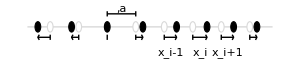

```mathematica
Block[{L=8,r=0.1,x},
x[i_]:=-0.5Cos[i π/6];
Graphics[{{LightGray,Line[{#,0}&/@{0.2,L+0.8}]},Translate[{{{EdgeForm[LightGray],White,Disk[{0,0},r]},{EdgeForm[Black],Disk[{x[#],0},r]}},{AbsoluteThickness[1],Line[{{0,-1.5r},{0,-2.5r}}],If[x[#]≠0,Line[{{{0,-2r},{x[#],-2r}},{{x[#]-0.5r Sign[x[#]],-1.5r},{x[#],-2r},{x[#]-0.5r Sign[x[#]],-2.5r}}}]]}},{#,0}]&/@Range[L],
Text["\!\(x\_\("<>#1<>"\)\)",{#2+x[#2]/2,-0.5}]&@@@{{"i-1",5},{"i",6},{"i+1",7}},
Translate[{AbsoluteThickness[1],Line[{{{0,0},{1,0}},{{0,-0.5r},{0,0.5r}},{{1,-0.5r},{1,0.5r}}}],Text["\!\(,a\)",{0.5,0},{0,-0.5}]},{3,2.5r}]},ImageSize->300]]
```

White dots - equilibrium positions R_i=i a.

Black dots - actual positions of atoms (the ith atom displaced by x_i).

The Hamiltonian in Eq. (DisplayFormulaNumbered) reduces to (as (R̂)_(i,j)=1 is trivial in 1D)

H=∑_i p_i^2/(2m)+∑_i κ/2(x_i-x_(i+1))^2.

or written as

H=∑_i p_i^2/(2m)+1/2∑_(i,j) x_i K_(i,j)x_j,

with

K_(i,j)=κ(2i,j-i,j+1-i,j-1).

Equation of motion:

m(x^(..))_i=-∑_j K_(i,j)x_j.

Derive the equation of motion Eq. (DisplayFormulaNumbered) from the Hamiltonian Eq. (DisplayFormulaNumbered).

From the Hamiltonian equation:

(ẋ)_i=(∂H)/(∂p_i)=p_i/m,
 (ṗ)_i=-(∂H)/(∂x_i)=-∑_j K_(i,j)x_j,

therefore

(x^(..))_i=((ṗ)_i)/m=-1/m∑_j K_(i,j)x_j.

Take the trial solution

x_i=u ⅇ^(-ⅈ ω t+ⅈ q R_i),

substitute into Eq. (DisplayFormulaNumbered),

-m ω^2 u ⅇ^(-ⅈ ω t+ⅈ q R_i)=-∑_j K_(i,j)u ⅇ^(-ⅈ ω t+ⅈ q R_j)

or

m ω^2=∑_j K_(i,j)ⅇ^(-ⅈ q (R_i-R_j))
=κ∑_j (2i,j-i,j+1-i,j-1)ⅇ^(-ⅈ q a (i-j))
=κ (2-ⅇ^(-ⅈ q a)-ⅇ^(+ⅈ q a))
=2κ (1-cos q a)
=κ (2 sin (q a)/2)^2.

Dispersion relation - the relationship between frequency (energy) and wavevector (momentum)

ω_q=2 √(κ/m)|sin(q a)/2|.

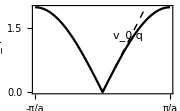

```mathematica
Plot[2 Abs[Sin[q/2]],{q,-π,π},PlotStyle->Black,Epilog->{{AbsoluteThickness[1],Dashed,Line[{{0,0},{2,2}}],Text["\!\(v\_0 q\)",{1.2,1.2},{0,-0.8},{1,2}]}},FrameLabel->{"\!\(q\)","\!\(ω\_q\)"},FrameTicks->{{Automatic,Automatic},{{π#1,If[Mod[#1,1]==0,Round[#1]"\!\(π/a\)",""],#3}&@@@Charting`ScaledTicks[{Identity,Identity}][-1,1],Automatic}},ImageSize->180]
```

Each point on the dispersion relation corresponds to a sound wave mode (a normal mode of the 1D lattice vibration). The sound wave quantum is called a phonon. The dispersion relation indicates that a phonon excitation of momentum ℏ q will carry energy ℏ ω_q.

It is sufficient to describe the dispersion relation within the first Brillouin zone [-π/a,π/a).

Because ω_q=ω_(q±(2π/a)) is periodic in the momentum space (with the same periodicity as the reciprocal lattice), the behavior of ω_q within the 1st BZ fully determines its behavior outside the 1st BZ.

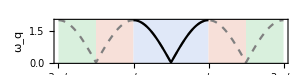

```mathematica
Show[{Plot[2 Abs[Sin[q/2]],{q,-3π,3π},PlotStyle->Directive[Dashed,Gray]],Plot[2 Abs[Sin[q/2]],{q,-π,π},PlotStyle->Black]},FrameLabel->{"\!\(q\)","\!\(ω\_q\)"},PlotRangePadding->{0,0.1},PlotRangeClipping->False,ImagePadding->{{Automatic,Automatic},{Automatic,20}},Prolog->{{Lighter[#1,0.85],Rectangle[{#2,-0.1},{#3,3}]}&@@@Thread[{{Green,Red,Blue,Blue,Red,Green},Most[#],Rest[#]}&@(π Range[-3,3])]},Epilog->{Translate[{#1 ,Text[#2,{0,0},{0,-0.6}]},{#3,2.2}]&@@@{{Blue,"1st BZ",0},{Red,"2nd",-3π/2},{Red,"2nd",3π/2},{Green,"3rd",-5π/2},{Green,"3rd",5π/2}}},FrameTicks->{{Automatic,Automatic},{{π#1,If[Mod[#1,1]==0,Round[#1]"\!\(π/a\)",""],#3}&@@@Charting`ScaledTicks[{Identity,Identity}][-3,3],Automatic}},AspectRatio->1/4,ImageSize->300]
```

Because q±(2π m/a) describe the same wave mode as q on the lattice (known as the aliasing of waves), there is no need to go beyond the 1st BZ.

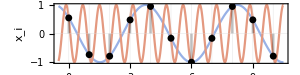

```mathematica
Block[{q=π/Sqrt[5],ϕ=π/Sqrt[10]},
Show[{Plot[{Cos[q i+ϕ],Cos[(q+2π)i+ϕ]},{i,-0.5,10.5},PlotStyle->(Lighter[#,0.5]&/@{Blue,Red})],DiscretePlot[Cos[q i+ϕ],{i,0,10},PlotStyle->Directive[Black,AbsolutePointSize[5]]]},AspectRatio->1/4,Axes->False,GridLines->{Range[0,10],{0}},FrameLabel->{"\!\(i\)","\!\(x\_i\)"},FrameTicks->{{Automatic,Automatic},{Range[0,10],None}},ImageSize->300]]
```

Group velocity - how fast a wave packet propagates

v_q=∂_q ω_q=(sgn q)/a √(κ/m)cos(q a)/2.

Low-frequency limit (BZ center): linear dispersion ω_q=v_0|q| ⇒ constant speed of sound

v_0=√(κ/m).

High-frequency limit (BZ boundary):

Group velocity vanishes at BZ boundary q=±π/a.

Inversion symmetry requires ω_q=ω_-q to be even in q, so its first order derivative v_q=∂_q ω_q must be odd in q, i.e. v_q=-v_-q. Further consider the periodicity v_q=v_(q-(2π/a)), we have v_(q-(2π/a))=-v_-q. Set q=π/a at the BZ boundary, this implies v_(-(π/a))=-v_(-(π/a)), thus v_(-(π/a))=0 (if v_q is smooth at the BZ boundary). Similar argument applies to v_(π/a)=0.

Bragg reflection: q=±π/a are related by a lattice momentum G=(2π)/a, strongly scattered to each other by the lattice ⇒ standing wave mode (equal-weight superposition of left- and right-moving modes):

ⅇ^(ⅈ (π/a)R_i)+ⅇ^(-ⅈ (π/a)R_i)∝(-)^i.

#### Acoustic and Optical Modes

Consider the lattice vibration of 1D diatomic chain, where two types of atoms of different masses (m_A and m_B) are arranged alternatively on a 1D lattice.

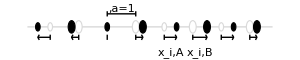

```mathematica
Block[{L=8,r=0.1,x},
x[i_]:=-0.5Cos[i π/6];
Graphics[{{LightGray,Line[{#,0}&/@{0.2,L+0.8}]},Translate[{{{EdgeForm[LightGray],White,Disk[{0,0},r(1+0.2(-1)^#)]},{EdgeForm[Black],Disk[{x[#],0},r(1+0.2(-1)^#)]}},{AbsoluteThickness[1],Line[{{0,-1.5r},{0,-2.5r}}],If[x[#]≠0,Line[{{{0,-2r},{x[#],-2r}},{{x[#]-0.5r Sign[x[#]],-1.5r},{x[#],-2r},{x[#]-0.5r Sign[x[#]],-2.5r}}}]]}},{#,0}]&/@Range[L],
Text["\!\(x\_\("<>#1<>"\)\)",{#2+x[#2]/2,-0.5}]&@@@{{"i,A",5},{"i,B",6}},
Translate[{AbsoluteThickness[1],Line[{{{0,0},{1,0}},{{0,-0.5r},{0,0.5r}},{{1,-0.5r},{1,0.5r}}}],Text["\!\(,a=1\)",{0.5,0},{0,-0.5}]},{3,2.5r}]},ImageSize->300]]
```

Equilibrium positions

R_(i,A)=2i,
R_(i,B)=2i+1.

Hamiltonian (based on Eq. (DisplayFormulaNumbered))

H=∑_i ((p_(i,A)^2)/(2 m_A)+(p_(i,B)^2)/(2 m_B))+κ/2∑_i ((x_(i,A)-x_(i,B))^2+(x_(i,B)-x_((i+1),A))^2).

Introduce the following vectors in each unit cell (taking A,B as basis)

p_i=(p_(i,A)
p_(i,B)),x_i=(x_(i,A)
x_(i,B)).

The Hamiltonian Eq. (DisplayFormulaNumbered) can be generally written as

H=1/2∑_(i,,j) (p_i ᵀ (M^-1)_(i,,j)p_j+x_i ᵀ K_(i,j)x_j),

where M and K matrices are

(M^-1)_(i,j)=(m_A^-1 δ_(i,j) | 0
0 | m_B^-1 δ_(i,j)),
K_(i,j)=κ(2 δ_(i,j) | -δ_(i,j)-δ_(i,j+1)
-δ_(i,j)-δ_(i,j-1) | 2 δ_(i,j)).

Equation of motion

∑_j M_(i,j)(x^(..))_j=-∑_j K_(i,j)x_j.

Take the trial solution (labeled by q)

x_i=(x_(i,A)
x_(i,B))=ⅇ^(-ⅈ ω t)(u_A ⅇ^(ⅈ q R_(i,A))
u_B ⅇ^(ⅈ q R_(i,B))),

substitute into Eq. (DisplayFormulaNumbered),

ω^2(m_A | 0
0 | m_B)(u_A
u_B)=2κ(1 | -cos q
-cos q | 1)(u_A
u_B)

Derive Eq. (DisplayFormulaNumbered).

Substitute Eq. (DisplayFormulaNumbered) into Eq. (DisplayFormulaNumbered)

lhs=∑_j M_(i,j)(x^(..))_j=∑_j M_(i,j)∂_t^2 ⅇ^(-ⅈ ω t)(u_A ⅇ^(ⅈ q R_(j,A))
u_B ⅇ^(ⅈ q R_(j,B))),
=-ω^2 ⅇ^(-ⅈ ω t)∑_j (m_A δ_(i,j) | 0
0 | m_B δ_(i,j))(u_A ⅇ^(ⅈ q (2j))
u_B ⅇ^(ⅈ q (2j+1)))
=-ω^2 ⅇ^(-ⅈ ω t)∑_j (m_A δ_(i,j)ⅇ^(ⅈ q (2j)) | 0
0 | m_B δ_(i,j)ⅇ^(ⅈ q (2j+1)))(u_A
u_B)
=-ω^2ⅇ^(-ⅈ ω t)(m_A ⅇ^(ⅈ q (2i)) | 0
0 | m_B ⅇ^(ⅈ q (2i+1)))(u_A
u_B)
=-ω^2ⅇ^(-ⅈ ω t+2ⅈ q i)(m_A | 0
0 | m_B ⅇ^(ⅈ q))(u_A
u_B),

rhs=-∑_j K_(i,j)x_j=-∑_j K_(i,j)ⅇ^(-ⅈ ω t)(u_A ⅇ^(ⅈ q R_(j,A))
u_B ⅇ^(ⅈ q R_(j,B)))
=-κ ⅇ^(-ⅈ ω t)∑_j (2 δ_(i,j) | -δ_(i,j)-δ_(i,j+1)
-δ_(i,j)-δ_(i,j-1) | 2 δ_(i,j))(u_A ⅇ^(ⅈ q (2j))
u_B ⅇ^(ⅈ q (2j+1)))
=-κ ⅇ^(-ⅈ ω t)∑_j (2 δ_(i,j)ⅇ^(ⅈ q (2j)) | (-δ_(i,j)-δ_(i,j+1))ⅇ^(ⅈ q (2j+1))
(-δ_(i,j)-δ_(i,j-1))ⅇ^(ⅈ q (2j)) | 2 δ_(i,j)ⅇ^(ⅈ q (2j+1)))(u_A
u_B)
=-κ ⅇ^(-ⅈ ω t)(2 ⅇ^(ⅈ q (2i)) | -ⅇ^(ⅈ q (2i+1))-ⅇ^(ⅈ q (2i-1))
-ⅇ^(ⅈ q (2i))-ⅇ^(ⅈ q (2i+2)) | 2 ⅇ^(ⅈ q (2i+1)))(u_A
u_B)
=-κ ⅇ^(-ⅈ ω t+2ⅈ q i)(2 | -ⅇ^(ⅈ q)-ⅇ^(-ⅈ q)
-1-ⅇ^(2ⅈ q) | 2 ⅇ^(ⅈ q))(u_A
u_B),

lhs=rhs ⇒

ω^2(m_A | 0
0 | m_B ⅇ^(ⅈ q))(u_A
u_B)=κ (2 | -ⅇ^(ⅈ q)-ⅇ^(-ⅈ q)
-1-ⅇ^(2ⅈ q) | 2 ⅇ^(ⅈ q))(u_A
u_B).

Multiply ⅇ^(-ⅈ q) on both side in the 2nd row,

ω^2(m_A | 0
0 | m_B)(u_A
u_B)=κ (2 | -ⅇ^(ⅈ q)-ⅇ^(-ⅈ q)
-ⅇ^(-ⅈ q)-ⅇ^(ⅈ q) | 2)(u_A
u_B)
=2κ (1 | -cos q
-cos q | 1)(u_A
u_B).

Dispersion relation: solving the (generalized) eigen problem [Reference] of Eq. (DisplayFormulaNumbered), two branches of solutions are found

ω_(q,±)=√(κ/(m_A m_B))(m_A+m_B±√(m_A^2+m_B^2+2 m_A m_B cos(2q)))^(1/2)

```mathematica
Eigenvalues[{2κ{{1,-Cos[q]},{-Cos[q],1}},{{mA,0},{0,mB}}}]
```

{(mA κ+mB κ-√(mA^2 κ^2+mB^2 κ^2+2 mA mB κ^2 Cos[2 q]))/(mA mB),(mA κ+mB κ+√(mA^2 κ^2+mB^2 κ^2+2 mA mB κ^2 Cos[2 q]))/(mA mB)}

Eigenvalues.

For κ=1, m_A=1, m_B=2:

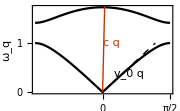

```mathematica
Block[{κ=1,mA=1,mB=2},
Plot[{Sqrt[κ/(mA mB)(mA+mB-Sqrt[mA^2+mB^2+2mA mB Cos[2q]])],Sqrt[κ/(mA mB)(mA+mB+Sqrt[mA^2+mB^2+2mA mB Cos[2q]])]},{q,-π/2,π/2},PlotStyle->Black,Epilog->{{AbsoluteThickness[1],{Dashed,Line[{{0,0},{1/Sqrt[2κ/(mA+mB)],1}}],Text["\!\(v\_0 q\)",0.5{1/Sqrt[2κ/(mA+mB)],1},{0,0.8},{1,1}]},{Red,Line[{{0,0},{0.05,1.8}}],Text["\!\(c q\)",{0,1},{-1.5,0}]}}},FrameLabel->{"\!\(q\)","\!\(ω\_q\)"},FrameTicks->{{Automatic,Automatic},{{π#1,If[Mod[2#,1]==0,π Rationalize[#1]],#3}&@@@Charting`ScaledTicks[{Identity,Identity}][-1/2,1/2],Automatic}},ImageSize->180]]
```

Acoustic phonon: the lower branch ω_(q,-) phonon modes (sound waves). 
Definition: the branch that exhibits a linear dispersion as q→0 (ω_(q->0) is vanishing).

ω_(q->0,-)=v_0|q|,
v_0=√((2κ)/(m_A+m_B)).

Optical phonon: the upper branch ω_(q,+) phonon modes (sound waves). 
Definition: the branch that maintains a finite frequency (ω_(q->0) is non-vanishing), such that the mode can possibly couples to light (photon). Because the speed of light c is much larger than the speed of sound v_0, such that the photon can transfer its energy-momentum to phonon only in the optical branch (hence the name “optical”).

There is a spectral gap between the two branches of sound waves.

Mode wave functions - take the eigen vector (u_A,u_B)ᵀ at a given momentum q on a given branch, reconstruct

x_(i,A)=u_A ⅇ^(-ⅈ ω_(q,±) t+ⅈ q R_(i,A)), x_(i,B)=u_B ⅇ^(-ⅈ ω_(q,±) t+ⅈ q R_(i,B))

Acoustic mode at q=0 (BZ center),

eigen value:ω_(0,-)=0,
eigen vector:(u_A
u_B)∝(1
1),

meaning that

x_(i,A)=x_(i,B)=u,

which corresponds to a mode that translate all atoms uniformly (the long-wave length limit of sound wave).

Acoustic mode at q=π/2 (BZ boundary), (assuming m_A<m_B)

eigen value:ω_(π/2,-)=√((2κ)/m_B),
eigen vector:(u_A
u_B)∝(0
1),

meaning that only B atoms oscillate

x_(i,A)=0, x_(i,B)=u ⅇ^(-ⅈ ω_(π/2,-) t+ⅈ π/2 R_(i,B)).

```mathematica
DynamicModule[{L=8,r=0.1,t=0,dt=0,x},
x[i_]:=If[EvenQ[i],0.3Cos[t+i π/2],0];
EventHandler[Dynamic[t+=dt;Graphics[{{LightGray,Line[{#,0}&/@{0.2,L+0.8}]},Translate[{{{EdgeForm[Black],Disk[{x[#],0},r(1+0.2(-1)^#)]}},{AbsoluteThickness[1],Line[{{0,-1.5r},{0,-2.5r}}],If[x[#]≠0,Line[{{{0,-2r},{x[#],-2r}},{{x[#]-0.5r Sign[x[#]],-1.5r},{x[#],-2r},{x[#]-0.5r Sign[x[#]],-2.5r}}}]]}},{#,0}]&/@Range[L]},ImageSize->300]],"MouseClicked":>If[dt>0,dt=0,dt=0.05π]]]
```

Optical mode at q=π/2 (BZ boundary), (assuming m_A<m_B)

eigen value:ω_(π/2,+)=√((2κ)/m_A),
eigen vector:(u_A
u_B)∝(1
0),

meaning that only A atoms oscillate

x_(i,A)=u ⅇ^(-ⅈ ω_(π/2,+) t+ⅈ π/2 R_(i,A)),x_(i,B)=0.

```mathematica
DynamicModule[{L=8,r=0.1,t=0,dt=0,x},
x[i_]:=If[OddQ[i],0.3Sin[t+i π/2],0];
EventHandler[Dynamic[t+=dt;Graphics[{{LightGray,Line[{#,0}&/@{0.2,L+0.8}]},Translate[{{{EdgeForm[Black],Disk[{x[#],0},r(1+0.2(-1)^#)]}},{AbsoluteThickness[1],Line[{{0,-1.5r},{0,-2.5r}}],If[x[#]≠0,Line[{{{0,-2r},{x[#],-2r}},{{x[#]-0.5r Sign[x[#]],-1.5r},{x[#],-2r},{x[#]-0.5r Sign[x[#]],-2.5r}}}]]}},{#,0}]&/@Range[L]},ImageSize->300]],"MouseClicked":>If[dt>0,dt=0,dt=0.05π Sqrt[2]]]]
```

At the BZ boundary, the oscillation mode transfers from B site (heavy atom, slower) to A site (light atom, faster), leading to a jump in the oscillation frequency ⇒ explains the spectral gap.

Optical mode at q=0 (BZ center),

eigen value:ω_(0,+)=√(2κ(1/m_A+1/m_B)),
eigen vector:(u_A
u_B)∝(m_B
-m_A),

meaning that

x_(i,A)=m_B u ⅇ^(-ⅈ ω_(0,+) t),x_(i,B)=-m_Au ⅇ^(-ⅈ ω_(0,+) t).

```mathematica
DynamicModule[{L=8,r=0.1,t=0,dt=0,x},
x[i_]:=If[OddQ[i],0.3Cos[t],-0.15Cos[t]];
EventHandler[Dynamic[t+=dt;Graphics[{{LightGray,Line[{#,0}&/@{0.2,L+0.8}]},Translate[{{{EdgeForm[Black],Disk[{x[#],0},r(1+0.2(-1)^#)]}},{AbsoluteThickness[1],Line[{{0,-1.5r},{0,-2.5r}}],If[x[#]≠0,Line[{{{0,-2r},{x[#],-2r}},{{x[#]-0.5r Sign[x[#]],-1.5r},{x[#],-2r},{x[#]-0.5r Sign[x[#]],-2.5r}}}]]}},{#,0}]&/@Range[L]},ImageSize->300]],"MouseClicked":>If[dt>0,dt=0,dt=0.05π Sqrt[3]]]]
```

Eigendecomposition of a matrix. Wikipedia.

Consider a diatomic chain where the atom masses m are the same, but the bond elastic constants are alternating between κ_1 and κ_2, as described by 
H=1/(2m)∑_i (p_(i,A)^2+p_(i,B)^2)+1/2∑_i ((κ_1(x_(i,A)-x_(i,B)))^2+(κ_2(x_(i,B)-x_((i+1),A)))^2). 
(i) Find the phonon dispersion relation.
(ii) Determine the sound velocity as q->0 for acoustic phonons.

#### Longitudinal and Transverse Modes

Generalize to higher dimension. Consider identical atoms forming a 3D cubic lattice. Equilibrium positions are given by

R_n=n_1 a_1+n_2 a_2+n_3 a_3,
{ | a_1=(1,0,0)
a_2=(0,1,0)
a_3=(0,0,1).

Take the pairwise interaction model Eq. (DisplayFormulaNumbered) on nearest neighboring bonds, the Hamiltonian reads

H=∑_i p_i^2/(2m)+1/2∑_⟨i,j⟩ (κ_⊥ (x_i-x_j)^2+(κ_∥-κ_⊥)((R̂)_(i,j)·(x_i-x_j))^2 ).

A lattice site is labeled by the index i (or j), which is equivalent to the integer vector n∈ℤ^3. ⟨i,j⟩ denotes that (i,j) are across the nearest neighboring bond on the cubic lattice.

κ_∥ - parallel elastic constants of the bond (Young’s modulus),
κ_⊥ - perpendicular elastic constants of the bond (shear modulus),
such that suppose the bond (R̂)_(i,j) is along x-direction, the bond potential energy is given by

1/2(x_i-x_j)·(κ_∥ |   |  
  | κ_⊥ |  
  |   | κ_⊥)·(x_i-x_j),

similar for y- and z-directions (by cyclic permuting the diagonal).

Rewrite the Hamiltonian in the general form of Eq. (DisplayFormulaNumbered),

H=∑_i p_i^2/(2m)+1/2∑_(i,j) x_i·K_(i,j)·x_j,

The elastic tensor K_(i,j) reads

K_(i,j)=K_0 δ_(R_i,R_j)-∑_(l=1,2,3) K_l (δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l)),
K_0=2(κ_∥+2 κ_⊥)𝟙 ,
K_l=κ_⊥𝟙+(κ_∥-κ_⊥)a_l⊗a_l,

where 𝟙 stands for 3×3 identity matrix, and a_l⊗a_l is the tensor product of a_l (spanning the vector to a matrix). More explicitly

K_0=2(κ_∥+2 κ_⊥)(1 |   |  
  | 1 |  
  |   | 1),
K_1=(κ_∥ |   |  
  | κ_⊥ |  
  |   | κ_⊥),
K_2=(κ_⊥ |   |  
  | κ_∥ |  
  |   | κ_⊥),
K_3=(κ_⊥ |   |  
  | κ_⊥ |  
  |   | κ_∥).

Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).

Let x_(i,j)=x_i-x_j,

∑_⟨i,j⟩ (κ_⊥x_(i,j)^2+(κ_∥-κ_⊥)((R̂)_(i,j)·x_(i,j))^2 )
=1/2∑_(i,j) ∑_(l=1,2,3) (κ_⊥ x_(i,j)^2+(κ_∥-κ_⊥)((R̂)_(i,j)·x_(i,j))^2 )(δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l))
=1/2∑_(i,j) ∑_(l=1,2,3) (κ_⊥ x_(i,j)^2+(κ_∥-κ_⊥)(a_l·x_(i,j))^2 )(δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l))
=1/2∑_(i,j) ∑_(l=1,2,3) x_(i,j)·(κ_⊥ 𝟙+(κ_∥-κ_⊥)a_l⊗a_l )·x_(i,j) (δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l))

Define K_l=κ_⊥ 𝟙+(κ_∥-κ_⊥)a_l⊗a_l, Eq. (DisplayFormulaNumbered) becomes

=1/2∑_(i,j) ∑_(l=1,2,3) (x_i-x_j)·K_l·(x_i-x_j) (δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l))
=1/2∑_(i,j) ∑_(l=1,2,3) (x_i·K_l·x_i-x_i·K_l·x_j-x_j·K_l·x_i+x_j·K_l·x_j) (δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l))
=∑_(i,j) ∑_(l=1,2,3) (x_i·K_l·x_i-x_i·K_l·x_j) (δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l))
=∑_i ∑_(l=1,2,3) 2x_i·K_l·x_i-∑_(i,j) ∑_(l=1,2,3) x_i·K_l·x_j (δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l))

Define K_0=2∑_(l=1,2,3) K_l, Eq. (DisplayFormulaNumbered) becomes

=∑_i x_i·K_0·x_i-∑_(i,j) ∑_(l=1,2,3) x_i·K_l·x_j (δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l))
=∑_(i,j) x_i·K_0·x_j δ_(R_i,R_j)-∑_(i,j) ∑_(l=1,2,3) x_i·K_l·x_j (δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l))
=∑_(i,j) x_i·(K_0 δ_(R_i,R_j)-∑_(l=1,2,3) K_l(δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l)))·x_j.

To match ∑_(i,j) x_i·K_(i,j)·x_j, one concludes

K_(i,j)=K_0 δ_(R_i,R_j)-∑_(l=1,2,3) K_l(δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l)),

where

K_0=2∑_(l=1,2,3) K_l
=2∑_(l=1,2,3) (κ_⊥ 𝟙+(κ_∥-κ_⊥)a_l⊗a_l)
=2(3 κ_⊥ 𝟙+(κ_∥-κ_⊥)∑_(l=1,2,3) a_l⊗a_l)
=2(3 κ_⊥ 𝟙+(κ_∥-κ_⊥)𝟙)
=2(κ_∥+2 κ_⊥)𝟙.

Equation of motion:

m (x^(..))_i=-∑_j K_(i,j)·x_j.

Take the trial solution

x_i=u ⅇ^(-ⅈ ω t+ⅈ q·R_i),

substitute into Eq. (DisplayFormulaNumbered),

m ω^2 u =∑_j K_(i,j)·u ⅇ^(-ⅈ q·(R_i-R_j))
=∑_j (K_0 δ_(R_i,R_j)-∑_(l=1,2,3) K_l (δ_(R_i,R_j+a_l)+δ_(R_i,R_j-a_l)))·u ⅇ^(-ⅈ q·(R_i-R_j))
=(K_0-∑_(l=1,2,3) K_l (ⅇ^(-ⅈ q·a_l)+ⅇ^(ⅈ q·a_l)))·u 
=(K_0-∑_(l=1,2,3) 2 K_l cos(q·a_l))·u 
=K(q)·u,

given K_0 and K_l matrices in Eq. (DisplayFormulaNumbered),

K(q)=(K_x(q) |   |  
  | K_y(q) |  
  |   | K_z(q)),
K_x(q)=κ_∥ (2sin q_x/2)^2+κ_⊥ (2sin q_y/2)^2+κ_⊥ (2sin q_z/2)^2,
K_y(q)=κ_⊥ (2sin q_x/2)^2+κ_∥ (2sin q_y/2)^2+κ_⊥ (2sin q_z/2)^2,
K_z(q)=κ_⊥ (2sin q_x/2)^2+κ_⊥ (2sin q_y/2)^2+κ_∥ (2sin q_z/2)^2,

Dispersion relation: The eigen equation m ω^2 u =K(q)·u in Eq. (DisplayFormulaNumbered) has three eigen modes:

α= | x | y | z
u_α= | (1,0,0) | (0,1,0) | (0,0,1)
ω_(q,α)= | √((K_x(q))/m) | √((K_y(q))/m) | √((K_z(q))/m)

α labels the polarization of the phonon modes (sound waves) in the 3D solid.

Dispersion relation

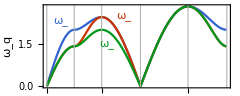

```mathematica
Block[{κ1=1,κ2=0.5,ωs},
ωs[{qx_,qy_,qz_}]:=Sqrt[{{κ1,κ2,κ2},{κ2,κ1,κ2},{κ2,κ2,κ1}}.(2{Sin[qx/2],Sin[qy/2],Sin[qz/2]})^2];
BZPlot[ωs,{"Γ","X","M","Γ","R","X"},BZRules->{"Γ"->{0,0,0},"X"->{π,0,0},"M"->{π,π,0},"R"->{π,π,π}},Epilog->{{#3,Text["\!\(ω\_\(q,"<>#1<>"\)\)",#2]}&@@@{{"x",{0.5π,2.3},Blue},{"y",{2.8π,2.5},Red},{"z",{2.2π,1.5},Green}}},FrameLabel->{None,"\!\(ω\_\(q\)\)"},AspectRatio->0.4,ImageSize->240]]
```

plotted along high symmetry lines in the cubic lattice Brillouin zone

```mathematica
Graphics3D[{{FaceForm[Opacity[0.2]],EdgeForm[AbsoluteThickness[1]],Cube[{0,0,0},2]},{Black,Rotate[Arrow[Tube[{{0,0,0},{2,0,0}}]],2π #/3,{1,1,1}]&/@{0,1,2},
Text["\!\(b\_"<>#1<>"\)",##2]&@@@{{"1",{2,0,0},{0.1,0.3}},{"2",{0,2,0},{1,0.8}},{"3",{0,0,2},{1.2,1}}}},
GraphicsComplex[{{0,0,0},{1,0,0},{1,1,0},{1,1,1}},{{AbsolutePointSize[6],Point[{1,2,3,4}]},{AbsoluteThickness[2],Line[{1,2,3,1,4,2}],Line[{4,3}]},{Text["Γ",1,{1,-0.5}],Text["X",2,{-0.5,1.2}],Text["M",3,{-1.5,0.2}],Text["R",4,{0.5,-0.8}]}}]},Boxed->False,ViewPoint->{5,2,3},Lighting->{{"Directional",White,{5,0,0}},{"Directional",White,{0,5,5}}},ImageSize->160]
```

-Graphics3D-

Longitudinal phonon: polarization parallel to momentum (u∥q)

Transverse phonon: polarization perpendicular to momentum (u⊥q)

Phonon modes along Γ-X, i.e. q=q(1,0,0),

Longitudinal mode (one branch)

ω_(q,x)=2 √((κ_∥)/m)|sin q/2|→^(q->0)v_L|q|.

Longitudinal speed of sound

v_L=√((κ_∥)/m).

Transverse mode (two branches)

ω_(q,y)=ω_(q,z)=2 √((κ_⊥)/m)|sin q/2|→^(q->0)v_T|q|.

Transverse speed of sound

v_T=√((κ_⊥)/m).

Phonon modes along Γ-M, i.e. q=q(1,1,0)/√2,

Longitudinal mode (one branch)

ω_(q,x+y)=2 √((κ_∥+κ_⊥)/(2m))|sin q/2|→^(q->0)v_L|q|.

Longitudinal speed of sound

v_L=√((κ_∥+κ_⊥)/(2m)).

Transverse mode (two branches)

ω_(q,x-y)=2 √((κ_∥+κ_⊥)/(2m))|sin q/2|→^(q->0)v_T1|q|,
ω_(q,z)=2 √((κ_⊥)/m)|sin q/2|→^(q->0)v_T2|q|.

Transverse speed of sound

v_T1=√((κ_∥+κ_⊥)/(2m)),
v_T2=√((κ_⊥)/m).

The degeneracy between v_L and v_T1 is accidental. Including further neighboring bonds in the model will lift this degeneracy.

### Specific Heat of Solid

#### Boltzmann Model

Specific heat (molar heat capacity): the rate that the average energy (per atom) increases with the raise of temperature.

c_V=(∂⟨ϵ⟩)/(∂T).

Specific heat often varies with temperature. Its temperature dependence reflects how energy is stored as excitations in the material.

How energy is stored in solid?

Boltzmann model: each atom in the solid sits in a harmonic well formed by the interaction with neighboring atoms.

Energy of a harmonic oscillator

ϵ(x,p)=1/(2m)p^2+κ/2 x^2.

The oscillation frequency is ω=√(κ/m).

Probability for the oscillator to be at the state (x,p) is

p(x,p)=1/Z ⅇ^(-β ϵ(x,p)),

where Z is the partition function (classical, canonical ensemble)

Z=∫ⅆ^D pⅆ^D x ⅇ^(-β ϵ(x,p))
=((2π m)/β)^(D/2)((2π)/(β κ))^(D/2)
=((2π)/(β ω))^D.

β=1/(k_B T): k_B - Boltzmann constant, T - temperature.

D - dimension of space.

Average energy

⟨ϵ⟩=∫ⅆ^D pⅆ^D xϵ(x,p)p(x,p)
=-∂_β ln Z
=D k_B T.

Specific heat

c_V=(∂⟨ϵ⟩)/(∂T)=D k_B.

For 3D materials (D=3),

c_V=3 k_B,

which is known as the Dulong-Petit law. Specific heats of some solids at room temperature and pressure:

Material | c_V/k_B |  
Gold (Au) | 3.05 |  
Antimony (Sb) | 3.03 |  
Zinc (Zn) | 3.02 |  
Iron (Fe) | 3.02 |  
Silver (Ag) | 2.99 |  
Lithium (Li) | 2.98 |  
Copper (Cu) | 2.94 |  
Aluminum (Al) | 2.91 |  
Diamond (C) | 0.735 | (why?)

The Dulong-Petit law works well for many crystalline materials above some characteristic temperature T_Θ around 200∼500K. Below this temperature scale T_Θ, it fails dramatically (for diamond, room temperature is already below its T_Θ). The specific heat is found to decrease with temperature rapidly towards zero as T→0.

#### Einstein Model

Einstein realized that quantum mechanics is important to understand the low-temperature behavior of specific heat.

Energy is quantized in quantum mechanics. For D-dimensional harmonic oscillator, its eigen energies (energy levels) are labeled by n∈ℕ^D,

ϵ_n=ℏ ω ∑_(i=1)^D (n_i+1/2).

ω - oscillator frequency,

ℏ - Planck constant.

Probability to find the oscillator in the ϵ_n energy level

p_n=1/Z ⅇ^(-β ϵ_n),

where Z is the partition function (quantum, canonical ensemble)

Z=∑_(n∈ℕ^D) ⅇ^(-β ϵ_n)
=(2sinh(β ℏ ω/2))^-D.

Evaluate the partition function in Eq. (DisplayFormulaNumbered).

Z=∑_(n∈ℕ^D) ⅇ^(-β ϵ_n)
=∑_(n∈ℕ^D) exp(-β ℏ ω ∑_(i=1)^D (n_i+1/2))
=∑_(n∈ℕ^D) ∏_(i=1)^D exp(-β ℏ ω (n_i+1/2))
=∏_(i=1)^D ∑_(n_i∈ℕ) ⅇ^(-β ℏ ω (n_i+1/2))
=∏_(i=1)^D (ⅇ^(-1/2β ℏ ω)∑_(n_i=0)^∞ ⅇ^(-β ℏ ω n_i))
=∏_(i=1)^D (ⅇ^(-1/2β ℏ ω)1/(1-ⅇ^(-β ℏ ω)))
=∏_(i=1)^D (1/(2sinh(β ℏ ω/2)))
=(2sinh(β ℏ ω/2))^-D.

Average energy

⟨ϵ⟩=∑_(n∈ℕ^D) ϵ_n p_n
=-∂_β ln Z
=(D ℏ ω)/2 coth((β ℏ ω)/2)
=D ℏ ω (n_B(β ℏ ω)+1/2),

n_B is the Bose-Einstein distribution function

n_B(β ℏ ω)=1/(ⅇ^(β ℏ ω)-1),

describing the average number of bosons occupying the mode of energy ℏ ω.

Specific heat

c_V=(∂⟨ϵ⟩)/(∂T)
=D k_B (((β ℏ ω)/2)csch((β ℏ ω)/2))^2.

Define a temperature scale (the Einstein temperature)

T_Θ=(ℏ ω)/k_B,

Eq. (DisplayFormulaNumbered) can be written as

c_V=D k_B ((T_Θ/(2T))csch(T_Θ/(2T)))^2.

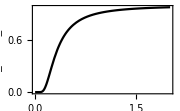

```mathematica
Off[General::munfl];Plot[(1/(2x)Csch[1/(2x)])^2,{x,0,2},PlotStyle->Black,FrameLabel->{"\!\(T/T\_Θ\)","\!\(c\_V/D k\_B\)"},ImageSize->180]
```

In the high-temperature limit (T≫T_Θ), the Dulong-Petit law c_V=D k_B is recovered.

However, at low-temperature (T≪T_Θ), the degrees of freedom “freeze out”. The energy level is discrete in quantum mechanics, when the temperature is too low compared to the excitation energy (the level spacing), the system will stuck in the ground state and can not absorb/release energy, hence no contribution to the specific heat.

#### Debye Model

The Einstein model takes into account the quantum effect. However, treating atoms in the solid as independent harmonic oscillators is a rather crude assumption. Debye further takes into account the fact that what really absorb/release energy in the solid are the collective excitations of atoms, i.e. phonons (sound waves).

Phonon can have different frequencies, as described by the dispersion relation ω_(q,α), which depends on:

q - phonon momentum,

α - phonon band index (including acoustic/optical branches, and different polarizations).

Following Eq. (DisplayFormulaNumbered), the specific heat should also average over all phonon modes

c_V=k_B/N∑_α ∑_(q∈BZ) (((β ℏ ω_(q,α))/2)csch((β ℏ ω_(q,α))/2))^2.

N - number of atoms, which is also the number of phonon modes (per polarization).

At low-temperature, focus on acoustic phonons, its dispersion can be modeled by

ω_q=v|q|,

where v is the speed of sound.

Here the dispersion is assumed to be isotropic, ignoring the velocity difference between longitudinal and transverse phonons.

The frequency is bounded as q varies in the Brillouin zone. So there must be some maximal frequency ω_max  (to be specified later).

Under the isotropic assumption, the momentum summation can be written as integration

1/N∑_α ∑_(q∈BZ)=D/N(L/(2π))^D∫ⅆ^D q
=(D Ω)/(2π)^D∫A_D q^(D-1)ⅆq
=∫(D A_D Ω)/(2π v)^D ω_q^(D-1)ⅆ ω_q
=∫ⅆ ω_q g(ω_q)

D - space dimension (also the number of polarizations α=1,…,D)

L - linear size of the system, which determined the momentum discretization unit (2π/L).

Ω - volume of unit cell.

A_D=2π^(D/2)/Γ(D/2) - area of a (D-1)-dimensional unit sphere (in the D-dimensional space).

Define the phonon density of state

g(ω)=(D A_D Ω)/(2π v)^D ω^(D-1)=(D^2 ω^(D-1))/ω_Θ^D,

where the Debye frequency ω_Θ is introduced as a frequency scale

ω_Θ^D=(D (2π v)^D)/(A_D Ω),

or more explicitly

ω_Θ=Piecewise[{{π/Ω v, D=1}, {((4π)/Ω)^(1/2)v, D=2}, {((6 π^2)/Ω)^(1/3)v, D=3}, {…, …}}]

```mathematica
Table[𝔇->PowerExpand[(𝔇(2π v)^𝔇/(2π^(𝔇/2)/Gamma[𝔇/2] Ω))],{𝔇,3}]
```

{1→(π v)/Ω,2→(4 π v^2)/Ω,3→(6 π^2 v^3)/Ω}

Enumerate ω_Θ.

The maximal frequency ω_max must be such that the density of state integrates to the number of polarization modes

D=∫_0^ω_max ⅆω g(ω)=D (ω_max/ω_Θ)^D,

so it turns out that the Debye frequency is also the maximal frequency ω_max=ω_Θ.

The specific heat Eq. (DisplayFormulaNumbered) can then be evaluated as

c_V=k_B ∫_0^ω_Θ ⅆω g(ω)(((β ℏ ω)/2)csch((β ℏ ω)/2))^2,

which can be organized as

c_V=D (k_B(T/T_Θ))^D Y(T_Θ/T),
Y(T_Θ/T)=D∫_0^(T_Θ/T) ⅆx  (x^(D-1)(x/2 csch(x/2)))^2.

T_Θ - Debye temperature, define as

T_Θ=(ℏ ω_Θ)/k_B.

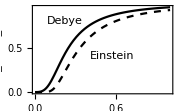

```mathematica
Block[{𝔇=3,Y,Cv},
Y[y_]:=𝔇 NIntegrate[x^(𝔇-1)(x/2 Csch[x/2])^2,{x,0,y}];
Cv[T_]:=T^𝔇 Y[1/T];
Plot[{Cv[T],(1/(2T)Csch[1/(2T)])^2},{T,0.001,1},PlotStyle->{Black,Directive[Black,Dashed]},FrameLabel->{"\!\(T/T\_Θ\)","\!\(c\_V/D k\_B\)"},Epilog->{Text["Debye",{0.22,0.8}],Text["Einstein",{0.57,0.4}]},ImageSize->180]]
```

Low-temperature limit T≪T_Θ,

The specific heat Eq. (DisplayFormulaNumbered) reads

c_V=D (k_B(T/T_Θ))^D Y(∞)
=(k_B(T/T_Θ))^D D^2 Γ(D+2)Li(D+1,1)

or more explicitly

c_V=k_B Piecewise[{{(T/T_Θ)π^2/3, D=1}, {(T/T_Θ)^2 24ζ(3), D=2}, {(T/T_Θ)^3(12 π^4)/5, D=3}, {…, …}}].

```mathematica
Table[𝔇->𝔇^2 Gamma[2+𝔇] PolyLog[1+𝔇,1],{𝔇,3}]
```

{1→π^2/3,2→24 Zeta[3],3→(12 π^4)/5}

Enumerate C_V.

In conclusion, the low-temperature specific heat from the acoustic phonon contribution scales with temperature as

c_V∼T^D,

which is c_V∼T^3 for D=3.

Suppose the dispersion of phonon is modified to ω_q∼(|q|)^z with some z>0 in D-dimensional space, determine the power-law exponent α that the specific heat c_V~T^α scales with temperature T in the low-temperature limit (as T→0).

### Stability of Crystal Order

#### Boltzmann Model

How much does an atom fluctuates around its equilibrium position in the solid?

Boltzmann model: each atom in the solid sits in a harmonic well formed by the interaction with neighboring atoms.

Energy of a harmonic oscillator

ϵ(x,p)=1/(2m)p^2+κ/2 x^2.

Probability for the oscillator to be at the state (x,p) is

p(x,p)=1/Z ⅇ^(-β ϵ(x,p)),

where Z is the partition function

Z=∫ⅆ^D pⅆ^D x ⅇ^(-β ϵ(x,p))
=((2π m)/β)^(D/2)((2π)/(β κ))^(D/2).

β=k_B T: k_B - Boltzmann constant, T - temperature.

D - dimension of space.

Variance of displacement

⟨x^2⟩=∫ⅆ^D pⅆ^D x x^2 p(x,p)
=-2/β∂_κ ln Z
=(D k_B T)/κ.

The result is consistent with the equal partition theorem, that the average energy stored in each quadratic term of the Hamiltonian is 1/2 k_B T. Thus, for harmonic oscillator the average potential energy should be

⟨1/2 κ x^2⟩=D/2 k_B T

Strictly speaking, the variance should be given by ⟨x^2⟩-⟨x⟩^2, but the first moment ⟨x⟩=0 vanishes due to the inversion symmetry ϵ(x,p)=ϵ(-x,p) of the harmonic oscillator.

Melting condition: If the displacement variance exceeds the squared atomic spacing a^2 of the lattice, the solid will melt.

⟨x^2⟩=(D k_B T)/κ>a^2⇒T>(κ a^2)/(D k_B)=T_*.

The melting temperature T_* is consistent with the rough estimate in Eq. (DisplayFormulaNumbered) T_*=E_bind/(N k_B), as E_bind∼N κ a^2.

However, this estimation did not takes into account the quantum effect and the collective nature of phonon excitations, and is wrong in low dimensions.

#### Einstein Model

The Einstein model includes the quantum effect of the harmonic oscillator.

Eigen energies of a D-dimensional harmonic oscillator (labeled by n∈ℕ^D)

ϵ_n=ℏ ω ∑_(i=1)^D (n_i+1/2).

ω=√(κ/m) - oscillator frequency.

ℏ - Planck constant.

Probability to find the oscillator in the ϵ_n energy level

p_n=1/Z ⅇ^(-β ϵ_n),

where Z is the partition function (quantum, canonical ensemble)

Z=∑_(n∈ℕ^D) ⅇ^(-β ϵ_n)
=(2sinh(β ℏ ω/2))^-D.

Variance of displacement on a particular eigenstate n

n x^2 n=2∂_κ ϵ_n.

Variance of displacement in the thermal ensemble

⟨x^2⟩=∑_(n∈ℕ^D) n x^2 n p_n
=∑_(n∈ℕ^D) 2(∂_κ ϵ_n)p_n
=-2/β∂_κ ln Z
=(D ℏ)/(2m ω)coth((β ℏ ω)/2)
=(D ℏ ω)/κ(n_B(β ℏ ω)+1/2).

Introduce the Einstein temperature following Eq. (DisplayFormulaNumbered)

T_Θ=(ℏ ω)/k_B,

the variance Eq. (DisplayFormulaNumbered) can be written as

⟨x^2⟩=x_Θ^2(n_B(T_Θ/T)+1/2),
 x_Θ^2=(D k_B T_Θ)/κ=(D ℏ)/(m ω).

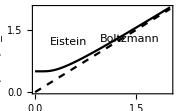

```mathematica
Plot[{1/(Exp[1/x]-1)+1/2,x},{x,0,2},PlotStyle->{Black,Directive[Black,Dashed]},FrameLabel->{"\!\(T/T\_Θ\)","\!\(⟨x\^2⟩/x\_Θ\%2\)"},Epilog->{Text["Eistein",{0.5,1.2}],Text["Boltzmann",{1.4,1.4},{0,1},{1,0.618}]},ImageSize->180]
```

At high temperature (T≫T_Θ), the linear temperature behavior is restored,

⟨x^2⟩=x_Θ^2(T/T_Θ)=(D k_B T)/κ,

matching the Boltzmann model Eq. (DisplayFormulaNumbered).

At low temperature (T≪T_Θ), the fluctuation saturates to a finite level

⟨x^2⟩=x_Θ^2/2=(D k_B T_Θ)/(2κ)=(D ℏ)/(2m ω).

This non-vanishing fluctuation at zero temperature is called the zero-point fluctuation, or the quantum fluctuation, originated from the uncertainty relation between position and momentum in quantum mechanics.

#### Debye Model

The Debye model further takes into account the collective nature of the phonon excitation in crystal, that the frequency ω_q vanishes with the momentum q for acoustic phonons, which leads to diverging fluctuation at long wave-length.

Define the average displacement variance of an atom in the solid

⟨x^2⟩=1/N∑_i ⟨x_i^2⟩.

Fourier transform to the momentum space

x_i=1/N^(1/2)∑_(q∈BZ) x_q ⅇ^(ⅈ q·R_i)

The fluctuation Eq. (DisplayFormulaNumbered) can be written as

⟨x^2⟩=1/N∑_(q∈BZ) ⟨x_q^†x_q⟩.

Each momentum q labels an independent acoustic phonon mode (for each polarization), for which x_q fluctuates as an independent harmonic oscillator.

Use the quantum result in Eq. (DisplayFormulaNumbered), and take the Debye model for density of state in Eq. (DisplayFormulaNumbered),

⟨x^2⟩=1/N∑_(q∈BZ) (D ℏ)/(2m ω_q)coth((β ℏ ω_q)/2)
=∫_0^ω_Θ ⅆω g(ω)ℏ/(2m ω)coth((β ℏ ω)/2),

which can be organized as

⟨x^2⟩=(x_Θ^2(T/T_Θ))^(D-1)Z(T_Θ/T),
x_Θ^2=(D^2 ℏ)/((D-2)m ω_Θ),
Z(T_Θ/T)=(D-2)∫_0^(T_Θ/T) ⅆx x^(D-2)/2 coth(x/2).

For D>2, at high temperature (T≫T_Θ), ⟨x^2⟩ approaches to the linear T behavior

⟨x^2⟩=x_Θ^2(T/T_Θ)=D/((D-2)m ω_Θ^2)D k_B T.

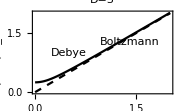

```mathematica
Block[{𝔇=3,Z},
Z[y_]:=NIntegrate[x^(𝔇-2)/2Coth[x/2],{x,0.y,y}];
Plot[{(𝔇-2)x^(𝔇-1) Z[1/x],x},{x,0.001,2},PlotStyle->{Black,Directive[Black,Dashed]},FrameLabel->{"\!\(T/T\_Θ\)","\!\(⟨x\^2⟩/x\_Θ\%2\)"},Epilog->{Text["Debye",{0.5,1.}],Text["Boltzmann",{1.4,1.4},{0,1},{1,0.618}]},PlotLabel->StringTemplate["\!\(D=`1`\)"][𝔇],ImageSize->180]]
```

In the zero temperature limit (T→0), the fluctuation saturates to

⟨x^2⟩=(D-2)/(2(D-1))x_Θ^2=(D^2 ℏ)/(2(D-1)m ω_Θ).

Derive Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

(i) In the high-temperature limit (T≫T_Θ), the integral limit T_Θ/T→0, so x is integrated in a small interval around 0 in the Z function. We can expand integrand around x→0, such that coth(x/2)=2/x+𝒪(x^0),

Z(T_Θ/T→0)=(D-2)∫_0^(T_Θ/T) ⅆx x^(D-2)/2 2/x
=(D-2)∫_0^(T_Θ/T) ⅆx x^(D-3)
= (x^(D-2))_(x=0)^(x=T_Θ/T)
=(T_Θ/T)^(D-2),

hence

⟨x^2⟩=(x_Θ^2(T/T_Θ))^(D-1)(T_Θ/T)^(D-2)
=x_Θ^2(T/T_Θ).

(ii) In the low-temperature limit (T≪T_Θ), the integral limit T_Θ/T→∞, so x≫1 part contributes to the majority of the integration in the Z function.  As x≫1, coth(x/2) can be approximate by 1,

Z(T_Θ/T→∞)=(D-2)∫_0^(T_Θ/T) ⅆx x^(D-2)/2
=(D-2)/(2(D-1))(x^(D-1))_(x=0)^(x=T_Θ/T)
=(D-2)/(2(D-1))(T_Θ/T)^(D-1),

hence

⟨x^2⟩=(x_Θ^2(T/T_Θ))^(D-1)(D-2)/(2(D-1))(T_Θ/T)^(D-1)
=(D-2)/(2(D-1))x_Θ^2.

For D=2, according to Eq. (DisplayFormulaNumbered), ⟨x^2⟩ diverges at any finite temperature ⇒ 2D crystals are inevitably melted by thermal fluctuations.
However, 2D crystals can still be stable at zero-temperature, as ⟨x^2⟩ remains finite in the T→0 limit for D=2 in Eq. (DisplayFormulaNumbered).

For D=1, according to Eq. (DisplayFormulaNumbered), ⟨x^2⟩ even diverges in the zero-temperature limit ⇒ 1D crystals are inevitably melted by quantum fluctuations.

Quantum-classical duality: a quantum system (T=0) at D dimension has properties similar to a classical system (T>0) at (D+1) dimension. This duality connects quantum mechanics with statistical mechanics in one higher dimension.

Suppose the dispersion of phonon is modified to ω_q∼(|q|)^z with some z>0 in D-dimensional space, determine 
(i) the critical dimension D_T that the crystal will melt by thermal fluctuation, 
(ii) the critical dimension D_Q that the crystal will melt by quantum fluctuation. 
(iii) Verify that the result is consistent with the generalized quantum-classical duality, that under a generic dynamical exponent z, a quantum system at D dimension will be dual to a classical system at (D+z) dimension.